# SoLID SIDIS Asymmetries

## Initialization

```mathematica
Clear["Global`*"];
```

## Format

```mathematica
Format[ϕh,TraditionalForm]:=StyleForm["ϕ_h",FontColor->Black];
Format[ϕS,TraditionalForm]:=StyleForm["ϕ_S",FontColor->Black];
Format[A0,TraditionalForm]:=StyleForm["A_0",FontColor->Blue];
Format[A1,TraditionalForm]:=StyleForm["A_1",FontColor->Blue];
Format[A2,TraditionalForm]:=StyleForm["A_2",FontColor->Blue];
Format[A3,TraditionalForm]:=StyleForm["A_3",FontColor->Blue];
Format[A4,TraditionalForm]:=StyleForm["A_4",FontColor->Blue];
Format[A5,TraditionalForm]:=StyleForm["A_5",FontColor->Blue];
Format[ω1,TraditionalForm]:=StyleForm["ω_1",FontColor->Darker[Blue,0.3]];
Format[ω2,TraditionalForm]:=StyleForm["ω_2",FontColor->Darker[Blue,0.3]];
Format[B0,TraditionalForm]:=StyleForm["B_0",FontColor->Darker[Red]];
Format[B1,TraditionalForm]:=StyleForm["B_1",FontColor->Darker[Red]];
Format[B2,TraditionalForm]:=StyleForm["B_2",FontColor->Darker[Red]];
Format[B3,TraditionalForm]:=StyleForm["B_3",FontColor->Darker[Red]];
Format[B4,TraditionalForm]:=StyleForm["B_4",FontColor->Darker[Red]];
Format[B5,TraditionalForm]:=StyleForm["B_5",FontColor->Darker[Red]];
Format[λ0,TraditionalForm]:=StyleForm["λ_0",FontColor->Darker[Orange]];
Format[λ1,TraditionalForm]:=StyleForm["λ_1",FontColor->Darker[Orange]];
Format[λ2,TraditionalForm]:=StyleForm["λ_2",FontColor->Darker[Orange]];
Format[λ3,TraditionalForm]:=StyleForm["λ_3",FontColor->Darker[Orange]];
Format[λ4,TraditionalForm]:=StyleForm["λ_4",FontColor->Darker[Orange]];
Format[λ5,TraditionalForm]:=StyleForm["λ_5",FontColor->Darker[Orange]];
Format[μ0,TraditionalForm]:=StyleForm["μ_0",FontColor->Darker[Orange]];
Format[μ1,TraditionalForm]:=StyleForm["μ_1",FontColor->Darker[Orange]];
Format[μ2,TraditionalForm]:=StyleForm["μ_2",FontColor->Darker[Orange]];
Format[μ3,TraditionalForm]:=StyleForm["μ_3",FontColor->Darker[Orange]];
Format[μ4,TraditionalForm]:=StyleForm["μ_4",FontColor->Darker[Orange]];
Format[μ5,TraditionalForm]:=StyleForm["μ_5",FontColor->Darker[Orange]];
Format[ξ0,TraditionalForm]:=StyleForm["ξ_0",FontColor->Darker[Orange]];
Format[ξ1,TraditionalForm]:=StyleForm["ξ_1",FontColor->Darker[Orange]];
Format[ξ2,TraditionalForm]:=StyleForm["ξ_2",FontColor->Darker[Orange]];
Format[ξ3,TraditionalForm]:=StyleForm["ξ_3",FontColor->Darker[Orange]];
Format[ξ4,TraditionalForm]:=StyleForm["ξ_4",FontColor->Darker[Orange]];
Format[ξ5,TraditionalForm]:=StyleForm["ξ_5",FontColor->Darker[Orange]];
Format[α0,TraditionalForm]:=StyleForm["α_0",FontColor->Darker[Orange]];
Format[α1,TraditionalForm]:=StyleForm["α_1",FontColor->Darker[Orange]];
Format[α2,TraditionalForm]:=StyleForm["α_2",FontColor->Darker[Orange]];
Format[α3,TraditionalForm]:=StyleForm["α_3",FontColor->Darker[Orange]];
Format[α4,TraditionalForm]:=StyleForm["α_4",FontColor->Darker[Orange]];
Format[α5,TraditionalForm]:=StyleForm["α_5",FontColor->Darker[Orange]];
Format[β0,TraditionalForm]:=StyleForm["β_0",FontColor->Darker[Orange]];
Format[β1,TraditionalForm]:=StyleForm["β_1",FontColor->Darker[Orange]];
Format[β2,TraditionalForm]:=StyleForm["β_2",FontColor->Darker[Orange]];
Format[β3,TraditionalForm]:=StyleForm["β_3",FontColor->Darker[Orange]];
Format[β4,TraditionalForm]:=StyleForm["β_4",FontColor->Darker[Orange]];
Format[β5,TraditionalForm]:=StyleForm["β_5",FontColor->Darker[Orange]];
Format[γ0,TraditionalForm]:=StyleForm["γ_0",FontColor->Darker[Orange]];
Format[γ1,TraditionalForm]:=StyleForm["γ_1",FontColor->Darker[Orange]];
Format[γ2,TraditionalForm]:=StyleForm["γ_2",FontColor->Darker[Orange]];
Format[γ3,TraditionalForm]:=StyleForm["γ_3",FontColor->Darker[Orange]];
Format[γ4,TraditionalForm]:=StyleForm["γ_4",FontColor->Darker[Orange]];
Format[γ5,TraditionalForm]:=StyleForm["γ_5",FontColor->Darker[Orange]];
Format[δ0,TraditionalForm]:=StyleForm["δ_0",FontColor->Darker[Orange]];
Format[δ1,TraditionalForm]:=StyleForm["δ_1",FontColor->Darker[Orange]];
Format[δ2,TraditionalForm]:=StyleForm["δ_2",FontColor->Darker[Orange]];
Format[δ3,TraditionalForm]:=StyleForm["δ_3",FontColor->Darker[Orange]];
Format[δ4,TraditionalForm]:=StyleForm["δ_4",FontColor->Darker[Orange]];
Format[δ5,TraditionalForm]:=StyleForm["δ_5",FontColor->Darker[Orange]];
Format[ϵ0,TraditionalForm]:=StyleForm["ϵ_0",FontColor->Darker[Orange]];
Format[ϵ1,TraditionalForm]:=StyleForm["ϵ_1",FontColor->Darker[Orange]];
Format[ϵ2,TraditionalForm]:=StyleForm["ϵ_2",FontColor->Darker[Orange]];
Format[ϵ3,TraditionalForm]:=StyleForm["ϵ_3",FontColor->Darker[Orange]];
Format[ϵ4,TraditionalForm]:=StyleForm["ϵ_4",FontColor->Darker[Orange]];
Format[ϵ5,TraditionalForm]:=StyleForm["ϵ_5",FontColor->Darker[Orange]];
Format[a,TraditionalForm]:=StyleForm["a",FontColor->Magenta];
Format[b,TraditionalForm]:=StyleForm["b",FontColor->Magenta];
```

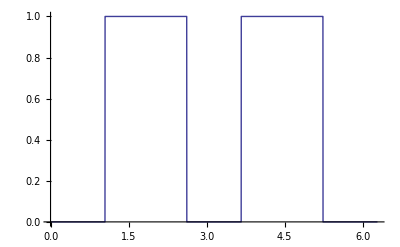

```mathematica
Plot[(HeavisideTheta[-((x-π)^2-a^2) ((x-π)^2-b^2)])/.{a->π/6,b->(2 π)/3},{x,0,2 π}]
```

```mathematica
HoldForm[B1","B2","B3","B4","B5]//TraditionalForm
```

B_1 , B_2 , B_3 , B_4 , B_5

```mathematica
Style["B_i",Darker[Red]]//TraditionalForm
```

B_i

## rad_len

radlen = 0.5 × rad × 4/3 + intrad
^3He 40cm 10amg: rad = 40 ÷ 67.42 × 1.345e-3 = 0.8e-3
intrad = (2 α)/π × ln E_e/m_e
X_0= (1432.8 A)/(Z (Z + 1) (11.319 - Log Z)) g·cm^-2
Radiation length = X_0/density

### Intrad

11 GeV e^-

```mathematica
Log[11.0/0.000511]*2/137/Pi
```

0.0463619

8.8 GeV e^-

```mathematica
Log[8.8/0.000511]*2/137/Pi
```

0.045325

### He-3 target

X_0

```mathematica
(1432.8 A)/(Z (Z + 1) (11.319 - Log[Z]))/.{A->3,Z->2}
```

67.4205

Radiation Length

```mathematica
67.42/(1.345*10^-3)
```

50126.4

rad

```mathematica
40/50126.4
```

0.000797983

radlen

```mathematica
0.5*0.0008*4/3+0.4636
0.5*0.0008*4/3+0.4533
```

0.464133

0.453833

### Proton target

NH_3

```mathematica
(*N*)
(1432.8 A)/(Z (Z + 1) (11.319 - Log[Z]))/.{A->14,Z->7}
(*H*)
(1432.8 A)/(Z (Z + 1) (11.319 - Log[Z]))/.{A->1,Z->1}
(*He*)
(1432.8 A)/(Z (Z + 1) (11.319 - Log[Z]))/.{A->4,Z->2}
```

38.2158

63.2918

89.894

```mathematica
(*N*)
38.2158/(0.917*14/17*0.55)
(*H*)
63.2918/(0.917*3/17*0.55)
(*He*)
89.894/(0.145*0.45)
```

92.0093

711.12

1377.69

Radiation Length

```mathematica
1/(1/92.0093+1/711.12+1/1377.69)
```

76.9198

rad

```mathematica
3/76.92
```

0.0390016

radlen

```mathematica
0.5*0.039*4/3+0.4636
0.5*0.039*4/3+0.4533
```

0.4896

0.4793

## Asymmetry

### cross section

```mathematica
sigma[ϕh_,ϕS_]:=σ (1+A1 Sin[ϕh-ϕS]+A2 Sin[ϕh+ϕS]+A3 Sin[3 ϕh-ϕS]+A4 Sin[ϕS]+A5 Sin[2 ϕh-ϕS]+ω1 Cos[ϕh]+ω2 Cos[2 ϕh]);
```

```mathematica
sigma[ϕh,ϕS]//TraditionalForm
```

σ (A_1 sin(ϕ_h-ϕ_S)+A_2 sin(ϕ_h+ϕ_S)+A_3 sin(3 ϕ_h-ϕ_S)+A_4 sin(ϕ_S)+A_5 sin(2 ϕ_h-ϕ_S)+ω_1 cos(ϕ_h)+ω_2 cos(2 ϕ_h)+1)

```mathematica
Integrate[(sigma[ϕh,ϕS]/.{ϕS->ϕh-ϕ}) Sin[ϕ],{ϕ,0,2 π}]//TraditionalForm
```

π σ (A_1+(A_3-A_2) cos(2 ϕ_h)+(A_5-A_4) cos(ϕ_h))

#### print

```mathematica
HoldForm[(d^2 σ)/(d ϕh d ϕS)==σ^– (1+ω1 Cos[ϕh]+ω2 Cos[2 ϕh]"\n                  "
+A1 Sin[ϕh-ϕS]+A2 Sin[ϕh+ϕS]+A3 Sin[3ϕh-ϕS]+A4 Sin[ϕS]+A5 Sin[2ϕh-ϕS])]//TraditionalForm
```

(d^2 σ)/(d ϕ_h d ϕ_S)==σ^– (1+ω_1 cos(ϕ_h)+ω_2 cos(2 ϕ_h) 
                  +A_1 sin(ϕ_h-ϕ_S)+A_2 sin(ϕ_h+ϕ_S)+A_3 sin(3 ϕ_h-ϕ_S)+A_4 sin(ϕ_S)+A_5 sin(2 ϕ_h-ϕ_S))

```mathematica
HoldForm[(d^2 N)/(d ϕh d ϕS)==N^– (1+f̃[ϕh,ϕS])]//TraditionalForm
```

(d^2 N)/(d ϕ_h d ϕ_S)==N^– (1+f̃(ϕ_h,ϕ_S))

```mathematica
HoldForm[(d^2 Ñ)/(d ϕh d ϕS)==Ñ (1+"F_1"[ω1,ω2] Cos[ϕh]+"F_2"[ω1,ω2] Cos[2 ϕh]"\n                  "
+B1 Sin[ϕh-ϕS]+B2 Sin[ϕh+ϕS]+B3 Sin[3ϕh-ϕS]+B4 Sin[ϕS]+B5 Sin[2ϕh-ϕS])]//TraditionalForm
```

(d^2 Ñ)/(d ϕ_h d ϕ_S)==Ñ (1+F_1(ω_1,ω_2) cos(ϕ_h)+F_2(ω_1,ω_2) cos(2 ϕ_h) 
                  +B_1 sin(ϕ_h-ϕ_S)+B_2 sin(ϕ_h+ϕ_S)+B_3 sin(3 ϕ_h-ϕ_S)+B_4 sin(ϕ_S)+B_5 sin(2 ϕ_h-ϕ_S))

```mathematica
Style[HoldForm["ϕ_h"==π],Blue]//TraditionalForm
```

ϕ_h==π

```mathematica
HoldForm[(d^2 σ)/(d ϕh d ϕS)==σ^– (1+f[ϕh,ϕS])]//TraditionalForm
```

```mathematica
HoldForm[(d σ)/(d ϕh)==σ^– (1+ω1 Cos[ϕh]+ω2 Cos[2 ϕh])]//TraditionalForm
```

(d σ)/(d ϕ_h)==σ^– (1+ω_1 cos(ϕ_h)+ω_2 cos(2 ϕ_h))

```mathematica
HoldForm[(d Ñ)/(d ϕh)==Ñ (1+B1 Cos[ϕh]+B2 Cos[2 ϕh] )]//TraditionalForm
```

(d Ñ)/(d ϕ_h)==Ñ (1+B_1 cos(ϕ_h)+B_2 cos(2 ϕ_h))

```mathematica
HoldForm[B1", "B2"and" ω1", "ω2]//TraditionalForm
```

B_1 ,  B_2 and ω_1 ,  ω_2

### one way

```mathematica
((2 Integrate[sigma[ϕh,ϕS] Sin[ϕh-ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])/Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])//TraditionalForm
```

A_1

```mathematica
((2 Integrate[sigma[ϕh,ϕS] Sin[ϕh+ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])/Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])//TraditionalForm
```

A_2

```mathematica
((2 Integrate[sigma[ϕh,ϕS] Sin[3 ϕh-ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])/Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])//TraditionalForm
```

A_3

```mathematica
((2 Integrate[sigma[ϕh,ϕS] Sin[ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])/Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])//TraditionalForm
```

A_4

```mathematica
((2 Integrate[sigma[ϕh,ϕS] Sin[2 ϕh-ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])/Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])//TraditionalForm
```

A_5

### another way

```mathematica
TraditionalForm[(π Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,ϕh-π,ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,ϕh,ϕh+π}],{ϕh,0,2 π}])/(2 Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])]
```

A_1

```mathematica
TraditionalForm[(π Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,-ϕh,-ϕh+π}]-Integrate[sigma[ϕh,ϕS],{ϕS,-ϕh-π,-ϕh}],{ϕh,0,2 π}])/(2 Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])]
```

A_2

```mathematica
TraditionalForm[(π Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,3 ϕh-π,3 ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,3 ϕh,3 ϕh+π}],{ϕh,0,2 π}])/(2 Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])]
```

A_3

```mathematica
TraditionalForm[(π Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,0,π}]-Integrate[sigma[ϕh,ϕS],{ϕS,-π,0}],{ϕh,0,2 π}])/(2 Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])]
```

A_4

```mathematica
TraditionalForm[(π Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,2 ϕh-π,2 ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,2 ϕh,2 ϕh+π}],{ϕh,0,2 π}])/(2 Integrate[sigma[ϕh,ϕS],{ϕh,0,2 π},{ϕS,0,2 π}])]
```

A_5

### UU

```mathematica
Clear[C1,C2]
```

```mathematica
(C1=Simplify[2 (Integrate[sigma[ϕh,ϕS] Cos[ϕh],{ϕh,a,π-b},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}]+Integrate[sigma[ϕh,ϕS] Cos[ϕh],{ϕh,π+b,2 π-a},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}])/(Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π}])]);
Collect[FullSimplify[Numerator[C1],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]/Collect[Simplify[Denominator[C1],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(2 ω_1 (-3 (a+b-π)-3 sin(a) cos(a)-3 sin(b) cos(b))+2 ω_2 (-3 sin(a)-sin(3 a)+3 sin(b)+sin(3 b))+2 (6 sin(b)-6 sin(a)))/(6 ω_1 (sin(b)-sin(a))+3 ω_2 (-sin(2 a)-sin(2 b))+3 (-2 a-2 b+2 π))

```mathematica
(C2=Simplify[2 (Integrate[sigma[ϕh,ϕS] Cos[2 ϕh],{ϕh,a,π-b},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}]+Integrate[sigma[ϕh,ϕS] Cos[2 ϕh],{ϕh,π+b,2 π-a},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}])/(Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π}])]);
Collect[FullSimplify[Numerator[C2],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]/Collect[Simplify[Denominator[C2],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(4 ω_1 (-3 sin(a)-sin(3 a)+3 sin(b)+sin(3 b))-3 ω_2 (4 (a+b-π)+sin(4 a)+sin(4 b))-12 (sin(2 a)+sin(2 b)))/(12 ω_1 (sin(b)-sin(a))+6 ω_2 (-sin(2 a)-sin(2 b))+6 (-2 a-2 b+2 π))

```mathematica
(eqUU1=(B1==(λ0+λ1 ω1+λ2 ω2)/(μ0+μ1 ω1+μ2 ω2)))//TraditionalForm
```

B_1==(λ_0+λ_1 ω_1+λ_2 ω_2)/(μ_0+μ_1 ω_1+μ_2 ω_2)

```mathematica
(eqUU2=(B2==(ξ0+ξ1 ω1+ξ2 ω2)/(μ0+μ1 ω1+μ2 ω2)))//TraditionalForm
```

B_2==(ξ_0+ξ_1 ω_1+ξ_2 ω_2)/(μ_0+μ_1 ω_1+μ_2 ω_2)

```mathematica
HoldForm[
λ0==4 (Sin[b]-Sin[a])"\n"
λ1==2 (π-a-b)-(Sin[2 a]+Sin[2 b])"\n"
λ2==2/3 (Sin[3b]-Sin[3 a])+2(Sin[b]-Sin[a])]//TraditionalForm
HoldForm[
ξ0==-2 (Sin[2a]+Sin[2b])==2μ2"\n"
ξ1==2/3 (Sin[3b]-Sin[3 a])+2(Sin[b]-Sin[a])==λ2"\n"
ξ2==2 (π-a-b)-1/2(Sin[4a]+Sin[4b])]//TraditionalForm
HoldForm[
μ0==2(π-a-b)"\n"
μ1==2(Sin[b]-Sin[a])"\n"
μ2==-(Sin[2a]+Sin[2b])]//TraditionalForm
```

λ_0==4 (sin(b)-sin(a)) 
 λ_1==2 (π-a-b)-(sin(2 a)+sin(2 b)) 
 λ_2==2/3 (sin(3 b)-sin(3 a))+2 (sin(b)-sin(a))

ξ_0==-2 (sin(2 a)+sin(2 b))==2 μ_2 
 ξ_1==2/3 (sin(3 b)-sin(3 a))+2 (sin(b)-sin(a))==λ_2 
 ξ_2==2 (π-a-b)-1/2 (sin(4 a)+sin(4 b))

μ_0==2 (π-a-b) 
 μ_1==2 (sin(b)-sin(a)) 
 μ_2==-(sin(2 a)+sin(2 b))

```mathematica
HoldForm["["a","π-b"]"∪"["π+b","2π-a"]"]//TraditionalForm
```

[ a , π-b ]∪[ π+b , 2 π-a ]

```mathematica
Solve[(eqUU1)&&(eqUU2(*/.{ξ1->λ2,ξ0->2 μ2}*)),{ω1,ω2}]//TraditionalForm
```

{{ω_1→-(-B_1 μ_0 ξ_2+B_1 μ_2 ξ_0-B_2 λ_0 μ_2+B_2 λ_2 μ_0+λ_0 ξ_2-λ_2 ξ_0)/(-B_1 μ_1 ξ_2+B_1 μ_2 ξ_1-B_2 λ_1 μ_2+B_2 λ_2 μ_1+λ_1 ξ_2-λ_2 ξ_1),ω_2→-(B_1 μ_0 ξ_1-B_1 μ_1 ξ_0+B_2 λ_0 μ_1-B_2 λ_1 μ_0-λ_0 ξ_1+λ_1 ξ_0)/(-B_1 μ_1 ξ_2+B_1 μ_2 ξ_1-B_2 λ_1 μ_2+B_2 λ_2 μ_1+λ_1 ξ_2-λ_2 ξ_1)}}

```mathematica
HoldForm[
(ω1==((μ0 ξ2-μ2 ξ0) B1-(μ0 λ2-μ2 λ0) B2-(λ0 ξ2-λ2 ξ0))/(-(μ1 ξ2-μ2 ξ1) B1+(μ1 λ2-μ2 λ1) B2+(λ1 ξ2-λ2 ξ1))) "\n"
(ω2==(-(μ0 ξ1-μ1 ξ0) B1+(μ0 λ1-μ1 λ0) B2+(λ0 ξ1-λ1 ξ0))/(-(μ1 ξ2-μ2 ξ1) B1+(μ1 λ2-μ2 λ1) B2+(λ1 ξ2-λ2 ξ1)))]//TraditionalForm
```

(ω_1==((μ_0 ξ_2-μ_2 ξ_0) B_1-(μ_0 λ_2-μ_2 λ_0) B_2-(λ_0 ξ_2-λ_2 ξ_0))/(-(μ_1 ξ_2-μ_2 ξ_1) B_1+(μ_1 λ_2-μ_2 λ_1) B_2+(λ_1 ξ_2-λ_2 ξ_1))) 
 (ω_2==(-(μ_0 ξ_1-μ_1 ξ_0) B_1+(μ_0 λ_1-μ_1 λ_0) B_2+(λ_0 ξ_1-λ_1 ξ_0))/(-(μ_1 ξ_2-μ_2 ξ_1) B_1+(μ_1 λ_2-μ_2 λ_1) B_2+(λ_1 ξ_2-λ_2 ξ_1)))

### UT

#### one way

```mathematica
Clear[C1,C2,C3,C4,C5]
```

```mathematica
(C1=Simplify[2 (Integrate[sigma[ϕh,ϕS] Sin[ϕh-ϕS],{ϕh,a,π-b},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}]+Integrate[sigma[ϕh,ϕS] Sin[ϕh-ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}])/(Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π}])]);
Collect[FullSimplify[Numerator[C1],Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C1],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(2 A_1 (-a-b+π)+2 A_2 (sin(a) cos(a)+sin(b) cos(b))+2 A_3 (sin(a) (-cos(a))-sin(b) cos(b))+2 A_4 (sin(a)-sin(b))+2 A_5 (sin(b)-sin(a)))/(2 ω_1 (sin(b)-sin(a))+ω_2 (-sin(2 a)-sin(2 b))-2 a-2 b+2 π)

```mathematica
(eqUT1=(HoldForm[B1==(α1 A1+α2 A2+α3 A3+α4 A4+α5 A5)/(μ0+μ1 ω1+μ2 ω2)]))//TraditionalForm
```

B_1==(α_1 A_1+α_2 A_2+α_3 A_3+α_4 A_4+α_5 A_5)/(μ_0+μ_1 ω_1+μ_2 ω_2)

```mathematica
HoldForm[
	α0==0"\n"
α1==2(π-a-b)"\n"
α2==Sin[2a]+Sin[2b]"\n"
α3==-(Sin[2a]+Sin[2b])"\n"
α4==-2(Sin[b]-Sin[a])"\n"
α5==2(Sin[b]-Sin[a])]//TraditionalForm
```

α_0==0 
 α_1==2 (π-a-b) 
 α_2==sin(2 a)+sin(2 b) 
 α_3==-(sin(2 a)+sin(2 b)) 
 α_4==-2 (sin(b)-sin(a)) 
 α_5==2 (sin(b)-sin(a))

```mathematica
(C2=Simplify[2 (Integrate[sigma[ϕh,ϕS] Sin[ϕh+ϕS],{ϕh,a,π-b},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}]+Integrate[sigma[ϕh,ϕS] Sin[ϕh+ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}])/(Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π}])]);
Collect[FullSimplify[Numerator[C2],Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C2],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(6 A_1 (sin(2 a)+sin(2 b))-12 A_2 (a+b-π)+3 A_3 (sin(4 a)+sin(4 b))+12 A_4 (sin(b)-sin(a))+A_5 (4 sin(3 a)-4 sin(3 b)))/(12 ω_1 (sin(b)-sin(a))+6 ω_2 (-sin(2 a)-sin(2 b))+6 (-2 a-2 b+2 π))

```mathematica
(eqUT2=(HoldForm[B2==(β1 A1+β2 A2+β3 A3+β4 A4+β5 A5)/(μ0+μ1 ω1+μ2 ω2)]))//TraditionalForm
```

B_2==(β_1 A_1+β_2 A_2+β_3 A_3+β_4 A_4+β_5 A_5)/(μ_0+μ_1 ω_1+μ_2 ω_2)

```mathematica
HoldForm[
	β0==0"\n"
β1==Sin[2a]+Sin[2b]"\n"
β2==2(π-a-b)"\n"
β3==1/2(Sin[4a]+Sin[4b])"\n"
β4==2(Sin[b]-Sin[a])"\n"
β5==-2/3(Sin[3b]-Sin[3a])]//TraditionalForm
```

β_0==0 
 β_1==sin(2 a)+sin(2 b) 
 β_2==2 (π-a-b) 
 β_3==1/2 (sin(4 a)+sin(4 b)) 
 β_4==2 (sin(b)-sin(a)) 
 β_5==-2/3 (sin(3 b)-sin(3 a))

```mathematica
(C3=Simplify[2 (Integrate[sigma[ϕh,ϕS] Sin[3 ϕh-ϕS],{ϕh,a,π-b},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}]+Integrate[sigma[ϕh,ϕS] Sin[3 ϕh-ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}])/(Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π}])]);
Collect[FullSimplify[Numerator[C3],Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C3],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(-6 A_1 (sin(2 a)+sin(2 b))+3 A_2 (sin(4 a)+sin(4 b))-12 A_3 (a+b-π)+A_4 (4 sin(3 a)-4 sin(3 b))+12 A_5 (sin(b)-sin(a)))/(12 ω_1 (sin(b)-sin(a))+6 ω_2 (-sin(2 a)-sin(2 b))+6 (-2 a-2 b+2 π))

```mathematica
(eqUT3=(HoldForm[B3==(γ1 A1+γ2 A2+γ3 A3+γ4 A4+γ5 A5)/(μ0+μ1 ω1+μ2 ω2)]))//TraditionalForm
```

B_3==(γ_1 A_1+γ_2 A_2+γ_3 A_3+γ_4 A_4+γ_5 A_5)/(μ_0+μ_1 ω_1+μ_2 ω_2)

```mathematica
HoldForm[
	γ0==0"\n"
γ1==-(Sin[2a]+Sin[2b])"\n"
γ2==1/2(Sin[4a]+Sin[4b])"\n"
γ3==2(π-a-b)"\n"
γ4==-2/3(Sin[3b]-Sin[3a])"\n"
γ5==2(Sin[b]-Sin[a])]//TraditionalForm
```

γ_0==0 
 γ_1==-(sin(2 a)+sin(2 b)) 
 γ_2==1/2 (sin(4 a)+sin(4 b)) 
 γ_3==2 (π-a-b) 
 γ_4==-2/3 (sin(3 b)-sin(3 a)) 
 γ_5==2 (sin(b)-sin(a))

```mathematica
(C4=Simplify[2 (Integrate[sigma[ϕh,ϕS] Sin[ϕS],{ϕh,a,π-b},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}]+Integrate[sigma[ϕh,ϕS] Sin[ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}])/(Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π}])]);
Collect[FullSimplify[Numerator[C4],Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C4],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(2 A_1 (3 sin(a)-3 sin(b))+2 A_2 (3 sin(b)-3 sin(a))+2 A_3 (sin(3 a)-sin(3 b))-6 A_4 (a+b-π)+2 A_5 (3 sin(a) cos(a)+3 sin(b) cos(b)))/(6 ω_1 (sin(b)-sin(a))+3 ω_2 (-sin(2 a)-sin(2 b))+3 (-2 a-2 b+2 π))

```mathematica
(eqUT4=(HoldForm[B4==(δ1 A1+δ2 A2+δ3 A3+δ4 A4+δ5 A5)/(μ0+μ1 ω1+μ2 ω2)]))//TraditionalForm
```

B_4==(δ_1 A_1+δ_2 A_2+δ_3 A_3+δ_4 A_4+δ_5 A_5)/(μ_0+μ_1 ω_1+μ_2 ω_2)

```mathematica
HoldForm[
	δ0==0"\n"
δ1==-2(Sin[b]-Sin[a])"\n"
δ2==2(Sin[b]-Sin[a])"\n"
δ3==-2/3(Sin[3b]-Sin[3a])"\n"
δ4==2(π-a-b)"\n"
δ5==Sin[2a]+Sin[2b]]//TraditionalForm
```

δ_0==0 
 δ_1==-2 (sin(b)-sin(a)) 
 δ_2==2 (sin(b)-sin(a)) 
 δ_3==-2/3 (sin(3 b)-sin(3 a)) 
 δ_4==2 (π-a-b) 
 δ_5==sin(2 a)+sin(2 b)

```mathematica
(C5=Simplify[2 (Integrate[sigma[ϕh,ϕS] Sin[2 ϕh-ϕS],{ϕh,a,π-b},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}]+Integrate[sigma[ϕh,ϕS] Sin[2 ϕh-ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π},Assumptions->{a>0,b>0,a+b<π}])/(Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2 π-a},{ϕS,0,2 π}])]);
Collect[FullSimplify[Numerator[C5],Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C5],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(2 A_1 (3 sin(b)-3 sin(a))+2 A_2 (sin(3 a)-sin(3 b))+2 A_3 (3 sin(b)-3 sin(a))+2 A_4 (3 sin(a) cos(a)+3 sin(b) cos(b))-6 A_5 (a+b-π))/(6 ω_1 (sin(b)-sin(a))+3 ω_2 (-sin(2 a)-sin(2 b))+3 (-2 a-2 b+2 π))

```mathematica
(eqUT5=(HoldForm[B5==(ϵ1 A1+ϵ2 A2+ϵ3 A3+ϵ4 A4+ϵ5 A5)/(μ0+μ1 ω1+μ2 ω2)]))//TraditionalForm
```

B_5==(ϵ_1 A_1+ϵ_2 A_2+ϵ_3 A_3+ϵ_4 A_4+ϵ_5 A_5)/(μ_0+μ_1 ω_1+μ_2 ω_2)

```mathematica
HoldForm[
	ϵ0==0"\n"
ϵ1==2(Sin[b]-Sin[a])"\n"
ϵ2==-2/3(Sin[3b]-Sin[3a])"\n"
ϵ3==2(Sin[b]-Sin[a])"\n"
ϵ4==Sin[2a]+Sin[2b]"\n"
ϵ5==2(π-a-b)]//TraditionalForm
```

ϵ_0==0 
 ϵ_1==2 (sin(b)-sin(a)) 
 ϵ_2==-2/3 (sin(3 b)-sin(3 a)) 
 ϵ_3==2 (sin(b)-sin(a)) 
 ϵ_4==sin(2 a)+sin(2 b) 
 ϵ_5==2 (π-a-b)

#### another way

```mathematica
Clear[C1,C2,C3,C4,C5];
```

```mathematica
TraditionalForm[C1=(π (Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,ϕh-π,ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,ϕh,ϕh+π}],{ϕh,a,π-b}]+Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,ϕh-π,ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,ϕh,ϕh+π}],{ϕh,π+b,2 π-a}]))/(2 (Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2π-a},{ϕS,0,2 π}]))];
Collect[FullSimplify[Numerator[C1],Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C1],Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(-2 A_1 (a+b-π)+A_2 (sin(2 a)+sin(2 b))+A_3 (-sin(2 a)-sin(2 b))+2 A_4 (sin(a)-sin(b))-2 A_5 (sin(a)-sin(b)))/(2 ω_1 (sin(b)-sin(a))+ω_2 (-sin(2 a)-sin(2 b))-2 a-2 b+2 π)

```mathematica
TraditionalForm[C2=Simplify[(π (Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,-ϕh,-ϕh+π}]-Integrate[sigma[ϕh,ϕS],{ϕS,-ϕh-π,-ϕh}],{ϕh,a,π-b}]+Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,-ϕh,-ϕh+π}]-Integrate[sigma[ϕh,ϕS],{ϕS,-ϕh-π,-ϕh}],{ϕh,π+b,2 π-a}]))/(2 (Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2π-a},{ϕS,0,2 π}]))]];
Collect[FullSimplify[Numerator[C2]/6,Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C2]/6,Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(A_1 (-sin(2 a)-sin(2 b))+2 A_2 (a+b-π)+1/2 A_3 (-sin(4 a)-sin(4 b))+A_4 (2 sin(a)-2 sin(b))+A_5 (2/3 sin(3 b)-2/3 sin(3 a)))/(2 ω_1 (sin(a)-sin(b))+2 ω_2 (sin(a) cos(a)+sin(b) cos(b))+2 (a+b-π))

```mathematica
TraditionalForm[C3=Simplify[(π (Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,3 ϕh-π,3 ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,3 ϕh,3 ϕh+π}],{ϕh,a,π-b}]+Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,3 ϕh-π,3 ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,3 ϕh,3 ϕh+π}],{ϕh,π+b,2 π-a}]))/(2 (Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2π-a},{ϕS,0,2 π}]))]];
Collect[FullSimplify[Numerator[C3]/6,Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C3]/6,Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(A_1 (sin(2 a)+sin(2 b))+1/2 A_2 (-sin(4 a)-sin(4 b))+2 A_3 (a+b-π)+2/3 A_4 (sin(3 b)-sin(3 a))+A_5 (2 sin(a)-2 sin(b)))/(2 ω_1 (sin(a)-sin(b))+2 ω_2 (sin(a) cos(a)+sin(b) cos(b))+2 (a+b-π))

```mathematica
TraditionalForm[C4=Simplify[(π (Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,0,π}]-Integrate[sigma[ϕh,ϕS],{ϕS,-π,0}],{ϕh,a,π-b}]+Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,0,π}]-Integrate[sigma[ϕh,ϕS],{ϕS,-π,0}],{ϕh,π+b,2 π-a}]))/(2 (Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2π-a},{ϕS,0,2 π}]))]];
Collect[FullSimplify[Numerator[C4]/3,Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C4]/3,Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(2 A_1 (sin(a)-sin(b))-2 A_2 (sin(a)-sin(b))+1/3 A_3 (2 sin(3 a)-2 sin(3 b))-2 A_4 (a+b-π)+A_5 (sin(2 a)+sin(2 b)))/(2 ω_1 (sin(b)-sin(a))+ω_2 (-sin(2 a)-sin(2 b))-2 a-2 b+2 π)

```mathematica
TraditionalForm[C5=Simplify[(π (Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,2 ϕh-π,2 ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,2 ϕh,2 ϕh+π}],{ϕh,a,π-b}]+Integrate[Integrate[sigma[ϕh,ϕS],{ϕS,2 ϕh-π,2 ϕh}]-Integrate[sigma[ϕh,ϕS],{ϕS,2 ϕh,2 ϕh+π}],{ϕh,π+b,2 π-a}]))/(2 (Integrate[sigma[ϕh,ϕS],{ϕh,a,π-b},{ϕS,0,2 π}]+Integrate[sigma[ϕh,ϕS],{ϕh,π+b,2π-a},{ϕS,0,2 π}]))]];
Collect[FullSimplify[Numerator[C5]/3,Assumptions->{a>0,b>0,a+b<π}],{A1,A2,A3,A4,A5}]/Collect[Simplify[Denominator[C5]/3,Assumptions->{a>0,b>0,a+b<π}],{ω1,ω2}]//TraditionalForm
```

(-2 A_1 (sin(a)-sin(b))+1/3 A_2 (2 sin(3 a)-2 sin(3 b))-2 A_3 (sin(a)-sin(b))+A_4 (sin(2 a)+sin(2 b))-2 A_5 (a+b-π))/(2 ω_1 (sin(b)-sin(a))+ω_2 (-sin(2 a)-sin(2 b))-2 a-2 b+2 π)

#### another another way

```mathematica
sigma[ϕh,ϕS]
```

σ (1+ω1 Cos[ϕh]+ω2 Cos[2 ϕh]+A1 Sin[ϕh-ϕS]+A5 Sin[2 ϕh-ϕS]+A3 Sin[3 ϕh-ϕS]+A4 Sin[ϕS]+A2 Sin[ϕh+ϕS])

```mathematica
(D1=Simplify[(Integrate[sigma[ϕh,ϕS] ,{ϕS,ϕh,ϕh+π}]-Integrate[sigma[ϕh,ϕS] ,{ϕS,ϕh+π,ϕh+2 π}])/(Integrate[sigma[ϕh,ϕS] ,{ϕS,ϕh,ϕh+π}]+Integrate[sigma[ϕh,ϕS] ,{ϕS,ϕh+π,ϕh+2 π}]),Assumptions->{a>0,b>0,a+b<π,ω1==0,ω2==0}])//TraditionalForm
```

-(2 (A_1+(A_3-A_2) cos(2 ϕ_h)+(A_5-A_4) cos(ϕ_h)))/π

```mathematica
(Integrate[sigma[ϕh,ϕS]-sigma[ϕh,-ϕS],{ϕh,a,π-b}])//TraditionalForm
```

1/3 σ sin(ϕ_S) (6 (A_1-A_2) (sin(a)-sin(b))-6 A_4 (a+b-π)+3 A_5 (sin(2 a)+sin(2 b))+2 A_3 sin(3 a)-2 A_3 sin(3 b))

#### inverse

```mathematica
Solve[((B1==(α1 A1+α2 A2+α3 A3)/(μ0+μ1 ω1+μ2 ω2))&&(B2==(β1 A1+β2 A2+β3 A3)/(μ0+μ1 ω1+μ2 ω2))&&(B3==(γ1 A1+γ2 A2+γ3 A3)/(μ0+μ1 ω1+μ2 ω2)))/.{μ0+μ1 ω1+μ2 ω2->1},{A1,A2,A3}]//TraditionalForm
```

{{A_1→-(B_1 β_2 γ_3-B_1 β_3 γ_2-α_2 B_2 γ_3+α_3 B_2 γ_2+α_2 β_3 B_3+α_3 β_2 (-B_3))/(-α_1 β_2 γ_3+α_1 β_3 γ_2+α_2 β_1 γ_3-α_2 β_3 γ_1-α_3 β_1 γ_2+α_3 β_2 γ_1),A_2→-(-β_1 B_1 γ_3+B_1 β_3 γ_1+α_1 B_2 γ_3-α_3 B_2 γ_1-α_1 β_3 B_3+α_3 β_1 B_3)/(-α_1 β_2 γ_3+α_1 β_3 γ_2+α_2 β_1 γ_3-α_2 β_3 γ_1-α_3 β_1 γ_2+α_3 β_2 γ_1),A_3→-(-β_1 B_1 γ_2+B_1 β_2 γ_1+α_1 B_2 γ_2-α_2 B_2 γ_1-α_1 β_2 B_3+α_2 β_1 B_3)/(α_1 β_2 γ_3-α_1 β_3 γ_2-α_2 β_1 γ_3+α_2 β_3 γ_1+α_3 β_1 γ_2-α_3 β_2 γ_1)}}

```mathematica
Numerator[Inverse[({{α1, α2, α3}, {β1, β2, β3}, {γ1, γ2, γ3}})]]//TraditionalForm
```

(β_2 γ_3-β_3 γ_2 | α_3 γ_2-α_2 γ_3 | α_2 β_3-α_3 β_2
β_3 γ_1-β_1 γ_3 | α_1 γ_3-α_3 γ_1 | α_3 β_1-α_1 β_3
β_1 γ_2-β_2 γ_1 | α_2 γ_1-α_1 γ_2 | α_1 β_2-α_2 β_1)

```mathematica
Denominator[Inverse[({{α1, α2, α3}, {β1, β2, β3}, {γ1, γ2, γ3}})]][[1,1]]//TraditionalForm
```

α_1 β_2 γ_3-α_1 β_3 γ_2-α_2 β_1 γ_3+α_2 β_3 γ_1+α_3 β_1 γ_2-α_3 β_2 γ_1

```mathematica
Denominator[Inverse[({{α1, α2, α3, α4, α5}, {β1, β2, β3, β4, β5}, {γ1, γ2, γ3, γ4, γ5}, {δ1, δ2, δ3, δ4, δ5}, {ϵ1, ϵ2, ϵ3, ϵ4, ϵ5}})]][[1,1]]//TraditionalForm
```

α_1 β_2 γ_3 δ_4 ϵ_5-α_1 β_2 γ_3 δ_5 ϵ_4-α_1 β_2 γ_4 δ_3 ϵ_5+α_1 β_2 γ_4 δ_5 ϵ_3+α_1 β_2 γ_5 δ_3 ϵ_4-α_1 β_2 γ_5 δ_4 ϵ_3-α_1 β_3 γ_2 δ_4 ϵ_5+α_1 β_3 γ_2 δ_5 ϵ_4+α_1 β_3 γ_4 δ_2 ϵ_5-α_1 β_3 γ_4 δ_5 ϵ_2-α_1 β_3 γ_5 δ_2 ϵ_4+α_1 β_3 γ_5 δ_4 ϵ_2+α_1 β_4 γ_2 δ_3 ϵ_5-α_1 β_4 γ_2 δ_5 ϵ_3-α_1 β_4 γ_3 δ_2 ϵ_5+α_1 β_4 γ_3 δ_5 ϵ_2+α_1 β_4 γ_5 δ_2 ϵ_3-α_1 β_4 γ_5 δ_3 ϵ_2-α_1 β_5 γ_2 δ_3 ϵ_4+α_1 β_5 γ_2 δ_4 ϵ_3+α_1 β_5 γ_3 δ_2 ϵ_4-α_1 β_5 γ_3 δ_4 ϵ_2-α_1 β_5 γ_4 δ_2 ϵ_3+α_1 β_5 γ_4 δ_3 ϵ_2-α_2 β_1 γ_3 δ_4 ϵ_5+α_2 β_1 γ_3 δ_5 ϵ_4+α_2 β_1 γ_4 δ_3 ϵ_5-α_2 β_1 γ_4 δ_5 ϵ_3-α_2 β_1 γ_5 δ_3 ϵ_4+α_2 β_1 γ_5 δ_4 ϵ_3+α_2 β_3 γ_1 δ_4 ϵ_5-α_2 β_3 γ_1 δ_5 ϵ_4-α_2 β_3 γ_4 δ_1 ϵ_5+α_2 β_3 γ_4 δ_5 ϵ_1+α_2 β_3 γ_5 δ_1 ϵ_4-α_2 β_3 γ_5 δ_4 ϵ_1-α_2 β_4 γ_1 δ_3 ϵ_5+α_2 β_4 γ_1 δ_5 ϵ_3+α_2 β_4 γ_3 δ_1 ϵ_5-α_2 β_4 γ_3 δ_5 ϵ_1-α_2 β_4 γ_5 δ_1 ϵ_3+α_2 β_4 γ_5 δ_3 ϵ_1+α_2 β_5 γ_1 δ_3 ϵ_4-α_2 β_5 γ_1 δ_4 ϵ_3-α_2 β_5 γ_3 δ_1 ϵ_4+α_2 β_5 γ_3 δ_4 ϵ_1+α_2 β_5 γ_4 δ_1 ϵ_3-α_2 β_5 γ_4 δ_3 ϵ_1+α_3 β_1 γ_2 δ_4 ϵ_5-α_3 β_1 γ_2 δ_5 ϵ_4-α_3 β_1 γ_4 δ_2 ϵ_5+α_3 β_1 γ_4 δ_5 ϵ_2+α_3 β_1 γ_5 δ_2 ϵ_4-α_3 β_1 γ_5 δ_4 ϵ_2-α_3 β_2 γ_1 δ_4 ϵ_5+α_3 β_2 γ_1 δ_5 ϵ_4+α_3 β_2 γ_4 δ_1 ϵ_5-α_3 β_2 γ_4 δ_5 ϵ_1-α_3 β_2 γ_5 δ_1 ϵ_4+α_3 β_2 γ_5 δ_4 ϵ_1+α_3 β_4 γ_1 δ_2 ϵ_5-α_3 β_4 γ_1 δ_5 ϵ_2-α_3 β_4 γ_2 δ_1 ϵ_5+α_3 β_4 γ_2 δ_5 ϵ_1+α_3 β_4 γ_5 δ_1 ϵ_2-α_3 β_4 γ_5 δ_2 ϵ_1-α_3 β_5 γ_1 δ_2 ϵ_4+α_3 β_5 γ_1 δ_4 ϵ_2+α_3 β_5 γ_2 δ_1 ϵ_4-α_3 β_5 γ_2 δ_4 ϵ_1-α_3 β_5 γ_4 δ_1 ϵ_2+α_3 β_5 γ_4 δ_2 ϵ_1-α_4 β_1 γ_2 δ_3 ϵ_5+α_4 β_1 γ_2 δ_5 ϵ_3+α_4 β_1 γ_3 δ_2 ϵ_5-α_4 β_1 γ_3 δ_5 ϵ_2-α_4 β_1 γ_5 δ_2 ϵ_3+α_4 β_1 γ_5 δ_3 ϵ_2+α_4 β_2 γ_1 δ_3 ϵ_5-α_4 β_2 γ_1 δ_5 ϵ_3-α_4 β_2 γ_3 δ_1 ϵ_5+α_4 β_2 γ_3 δ_5 ϵ_1+α_4 β_2 γ_5 δ_1 ϵ_3-α_4 β_2 γ_5 δ_3 ϵ_1-α_4 β_3 γ_1 δ_2 ϵ_5+α_4 β_3 γ_1 δ_5 ϵ_2+α_4 β_3 γ_2 δ_1 ϵ_5-α_4 β_3 γ_2 δ_5 ϵ_1-α_4 β_3 γ_5 δ_1 ϵ_2+α_4 β_3 γ_5 δ_2 ϵ_1+α_4 β_5 γ_1 δ_2 ϵ_3-α_4 β_5 γ_1 δ_3 ϵ_2-α_4 β_5 γ_2 δ_1 ϵ_3+α_4 β_5 γ_2 δ_3 ϵ_1+α_4 β_5 γ_3 δ_1 ϵ_2-α_4 β_5 γ_3 δ_2 ϵ_1+α_5 β_1 γ_2 δ_3 ϵ_4-α_5 β_1 γ_2 δ_4 ϵ_3-α_5 β_1 γ_3 δ_2 ϵ_4+α_5 β_1 γ_3 δ_4 ϵ_2+α_5 β_1 γ_4 δ_2 ϵ_3-α_5 β_1 γ_4 δ_3 ϵ_2-α_5 β_2 γ_1 δ_3 ϵ_4+α_5 β_2 γ_1 δ_4 ϵ_3+α_5 β_2 γ_3 δ_1 ϵ_4-α_5 β_2 γ_3 δ_4 ϵ_1-α_5 β_2 γ_4 δ_1 ϵ_3+α_5 β_2 γ_4 δ_3 ϵ_1+α_5 β_3 γ_1 δ_2 ϵ_4-α_5 β_3 γ_1 δ_4 ϵ_2-α_5 β_3 γ_2 δ_1 ϵ_4+α_5 β_3 γ_2 δ_4 ϵ_1+α_5 β_3 γ_4 δ_1 ϵ_2-α_5 β_3 γ_4 δ_2 ϵ_1-α_5 β_4 γ_1 δ_2 ϵ_3+α_5 β_4 γ_1 δ_3 ϵ_2+α_5 β_4 γ_2 δ_1 ϵ_3-α_5 β_4 γ_2 δ_3 ϵ_1-α_5 β_4 γ_3 δ_1 ϵ_2+α_5 β_4 γ_3 δ_2 ϵ_1

```mathematica
Numerator[Inverse[({{α1, α2, α3, α4, α5}, {β1, β2, β3, β4, β5}, {γ1, γ2, γ3, γ4, γ5}, {δ1, δ2, δ3, δ4, δ5}, {ϵ1, ϵ2, ϵ3, ϵ4, ϵ5}})]][[1,1]]//TraditionalForm
```

β_2 γ_3 δ_4 ϵ_5-β_2 γ_3 δ_5 ϵ_4-β_2 γ_4 δ_3 ϵ_5+β_2 γ_4 δ_5 ϵ_3+β_2 γ_5 δ_3 ϵ_4-β_2 γ_5 δ_4 ϵ_3-β_3 γ_2 δ_4 ϵ_5+β_3 γ_2 δ_5 ϵ_4+β_3 γ_4 δ_2 ϵ_5-β_3 γ_4 δ_5 ϵ_2-β_3 γ_5 δ_2 ϵ_4+β_3 γ_5 δ_4 ϵ_2+β_4 γ_2 δ_3 ϵ_5-β_4 γ_2 δ_5 ϵ_3-β_4 γ_3 δ_2 ϵ_5+β_4 γ_3 δ_5 ϵ_2+β_4 γ_5 δ_2 ϵ_3-β_4 γ_5 δ_3 ϵ_2-β_5 γ_2 δ_3 ϵ_4+β_5 γ_2 δ_4 ϵ_3+β_5 γ_3 δ_2 ϵ_4-β_5 γ_3 δ_4 ϵ_2-β_5 γ_4 δ_2 ϵ_3+β_5 γ_4 δ_3 ϵ_2

```mathematica
Simplify[Numerator[Inverse[({{λ1, λ2, -λ2, -λ3, λ3}, {λ2, λ1, λ4, λ3, λ5}, {-λ2, λ4, λ1, λ5, λ3}, {-λ3, λ3, λ5, λ1, λ2}, {λ3, λ5, λ3, λ2, λ1}})]]]//TraditionalForm
```

(λ_1^4-(λ_2^2+2 λ_3^2+λ_4^2+2 λ_5^2) λ_1^2+4 λ_3 (λ_2+λ_4) λ_5 λ_1+λ_3^4+(λ_5^2-λ_2 λ_4)^2-2 λ_3^2 (λ_5^2+λ_2 λ_4) | -(-λ_2^2+λ_1 λ_2+λ_3 (λ_3-λ_5)) (λ_1^2+(λ_2+λ_4) λ_1-λ_3^2-λ_5^2+λ_2 λ_4-2 λ_3 λ_5) | (-λ_2^2+λ_1 λ_2+λ_3 (λ_3-λ_5)) (λ_1^2+(λ_2+λ_4) λ_1-λ_3^2-λ_5^2+λ_2 λ_4-2 λ_3 λ_5) | λ_3 λ_1^3+λ_2 (2 λ_3-λ_5) λ_1^2+((λ_3-λ_5) λ_2^2+λ_4 (λ_3-λ_5) λ_2-λ_3 (λ_3^2+2 λ_5 λ_3+λ_4^2+λ_5^2)) λ_1+λ_3 λ_4 (λ_3+λ_5)^2+λ_2^2 λ_4 (λ_3-λ_5)-λ_2 (λ_3^3+λ_5 λ_3^2+λ_4^2 λ_3-λ_5^2 λ_3-λ_5^3) | -λ_3 λ_1^3+λ_2 (λ_5-2 λ_3) λ_1^2+((λ_5-λ_3) λ_2^2+λ_4 (λ_5-λ_3) λ_2+λ_3 (λ_3^2+2 λ_5 λ_3+λ_4^2+λ_5^2)) λ_1-λ_3 λ_4 (λ_3+λ_5)^2+λ_2^2 λ_4 (λ_5-λ_3)+λ_2 (λ_3^3+λ_5 λ_3^2+λ_4^2 λ_3-λ_5^2 λ_3-λ_5^3)
-(-λ_2^2+λ_1 λ_2+λ_3 (λ_3-λ_5)) (λ_1^2+(λ_2+λ_4) λ_1-λ_3^2-λ_5^2+λ_2 λ_4-2 λ_3 λ_5) | λ_1^4-(2 λ_2^2+3 λ_3^2+λ_5^2) λ_1^2+4 λ_2 λ_3 (λ_5-λ_3) λ_1+λ_2^4+λ_3^2 (λ_3+λ_5)^2-2 λ_2^2 λ_3 (λ_3-λ_5) | λ_2^4-2 λ_3 (λ_3-λ_5) λ_2^2+2 λ_3^2 λ_4 λ_2-λ_3^2 (λ_3+λ_5)^2-λ_1^3 λ_4-λ_1^2 (λ_2^2-2 λ_3 λ_5)+λ_1 (λ_4 λ_2^2-(3 λ_3^2-2 λ_5 λ_3+λ_5^2) λ_2+2 λ_3^2 λ_4) | -λ_3 λ_1^3+(λ_4 λ_5+λ_2 (λ_5-λ_3)) λ_1^2+(2 λ_3^3+λ_5 λ_3^2-(λ_5^2+2 λ_2 λ_4) λ_3+λ_2^2 λ_5) λ_1-λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (3 λ_3^2+2 λ_5 λ_3-λ_5^2) | -λ_5 λ_1^3+λ_3 (2 λ_2+λ_4) λ_1^2+(λ_3^3+λ_5^3+λ_2 λ_4 (λ_3-λ_5)+λ_2^2 (2 λ_3+λ_5)) λ_1+λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (λ_3^2-2 λ_5 λ_3-3 λ_5^2)
(-λ_2^2+λ_1 λ_2+λ_3 (λ_3-λ_5)) (λ_1^2+(λ_2+λ_4) λ_1-λ_3^2-λ_5^2+λ_2 λ_4-2 λ_3 λ_5) | λ_2^4-2 λ_3 (λ_3-λ_5) λ_2^2+2 λ_3^2 λ_4 λ_2-λ_3^2 (λ_3+λ_5)^2-λ_1^3 λ_4-λ_1^2 (λ_2^2-2 λ_3 λ_5)+λ_1 (λ_4 λ_2^2-(3 λ_3^2-2 λ_5 λ_3+λ_5^2) λ_2+2 λ_3^2 λ_4) | λ_1^4-(2 λ_2^2+3 λ_3^2+λ_5^2) λ_1^2+4 λ_2 λ_3 (λ_5-λ_3) λ_1+λ_2^4+λ_3^2 (λ_3+λ_5)^2-2 λ_2^2 λ_3 (λ_3-λ_5) | -λ_5 λ_1^3+λ_3 (2 λ_2+λ_4) λ_1^2+(λ_3^3+λ_5^3+λ_2 λ_4 (λ_3-λ_5)+λ_2^2 (2 λ_3+λ_5)) λ_1+λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (λ_3^2-2 λ_5 λ_3-3 λ_5^2) | -λ_3 λ_1^3+(λ_4 λ_5+λ_2 (λ_5-λ_3)) λ_1^2+(2 λ_3^3+λ_5 λ_3^2-(λ_5^2+2 λ_2 λ_4) λ_3+λ_2^2 λ_5) λ_1-λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (3 λ_3^2+2 λ_5 λ_3-λ_5^2)
λ_3 λ_1^3+λ_2 (2 λ_3-λ_5) λ_1^2+((λ_3-λ_5) λ_2^2+λ_4 (λ_3-λ_5) λ_2-λ_3 (λ_3^2+2 λ_5 λ_3+λ_4^2+λ_5^2)) λ_1+λ_3 λ_4 (λ_3+λ_5)^2+λ_2^2 λ_4 (λ_3-λ_5)-λ_2 (λ_3^3+λ_5 λ_3^2+λ_4^2 λ_3-λ_5^2 λ_3-λ_5^3) | -λ_3 λ_1^3+(λ_4 λ_5+λ_2 (λ_5-λ_3)) λ_1^2+(2 λ_3^3+λ_5 λ_3^2-(λ_5^2+2 λ_2 λ_4) λ_3+λ_2^2 λ_5) λ_1-λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (3 λ_3^2+2 λ_5 λ_3-λ_5^2) | -λ_5 λ_1^3+λ_3 (2 λ_2+λ_4) λ_1^2+(λ_3^3+λ_5^3+λ_2 λ_4 (λ_3-λ_5)+λ_2^2 (2 λ_3+λ_5)) λ_1+λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (λ_3^2-2 λ_5 λ_3-3 λ_5^2) | λ_1^4-(2 λ_2^2+2 λ_3^2+λ_4^2+λ_5^2) λ_1^2-2 (λ_4 λ_2^2+λ_3 (λ_3-λ_5) λ_2-λ_3 λ_4 λ_5) λ_1+λ_3^2 λ_4^2+λ_2^2 (λ_3+λ_5)^2+2 λ_2 λ_3 λ_4 (λ_5-λ_3) | -λ_2 λ_1^3-λ_3 (λ_3-2 λ_5) λ_1^2+(2 λ_2^3+(-2 λ_3^2+2 λ_5 λ_3+λ_4^2) λ_2-λ_4 (λ_3^2+λ_5^2)) λ_1+λ_3^2 λ_4^2-λ_2^2 (λ_3+λ_5)^2+2 λ_2^3 λ_4+2 λ_2 λ_3 λ_4 (λ_5-λ_3)
-λ_3 λ_1^3+λ_2 (λ_5-2 λ_3) λ_1^2+((λ_5-λ_3) λ_2^2+λ_4 (λ_5-λ_3) λ_2+λ_3 (λ_3^2+2 λ_5 λ_3+λ_4^2+λ_5^2)) λ_1-λ_3 λ_4 (λ_3+λ_5)^2+λ_2^2 λ_4 (λ_5-λ_3)+λ_2 (λ_3^3+λ_5 λ_3^2+λ_4^2 λ_3-λ_5^2 λ_3-λ_5^3) | -λ_5 λ_1^3+λ_3 (2 λ_2+λ_4) λ_1^2+(λ_3^3+λ_5^3+λ_2 λ_4 (λ_3-λ_5)+λ_2^2 (2 λ_3+λ_5)) λ_1+λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (λ_3^2-2 λ_5 λ_3-3 λ_5^2) | -λ_3 λ_1^3+(λ_4 λ_5+λ_2 (λ_5-λ_3)) λ_1^2+(2 λ_3^3+λ_5 λ_3^2-(λ_5^2+2 λ_2 λ_4) λ_3+λ_2^2 λ_5) λ_1-λ_2^2 λ_3 λ_4-λ_2^3 (λ_3+λ_5)-λ_3^2 λ_4 (λ_3+λ_5)+λ_2 λ_3 (3 λ_3^2+2 λ_5 λ_3-λ_5^2) | -λ_2 λ_1^3-λ_3 (λ_3-2 λ_5) λ_1^2+(2 λ_2^3+(-2 λ_3^2+2 λ_5 λ_3+λ_4^2) λ_2-λ_4 (λ_3^2+λ_5^2)) λ_1+λ_3^2 λ_4^2-λ_2^2 (λ_3+λ_5)^2+2 λ_2^3 λ_4+2 λ_2 λ_3 λ_4 (λ_5-λ_3) | λ_1^4-(2 λ_2^2+2 λ_3^2+λ_4^2+λ_5^2) λ_1^2-2 (λ_4 λ_2^2+λ_3 (λ_3-λ_5) λ_2-λ_3 λ_4 λ_5) λ_1+λ_3^2 λ_4^2+λ_2^2 (λ_3+λ_5)^2+2 λ_2 λ_3 λ_4 (λ_5-λ_3))

```mathematica
Simplify[Denominator[Inverse[({{λ1, λ2, -λ2, -λ3, λ3}, {λ2, λ1, λ4, λ3, λ5}, {-λ2, λ4, λ1, λ5, λ3}, {-λ3, λ3, λ5, λ1, λ2}, {λ3, λ5, λ3, λ2, λ1}})][[1,1]]]]//TraditionalForm
```

-λ_1^3 (3 λ_2^2+4 λ_3^2+λ_4^2+2 λ_5^2)+λ_1^2 (8 λ_2 λ_3 λ_5-6 λ_2 λ_3^2-2 λ_2^2 λ_4+4 λ_3 λ_4 λ_5)+λ_1 (λ_2^2 (8 λ_3 λ_5-2 λ_3^2+λ_4^2+2 λ_5^2)-2 λ_2 λ_4 (-2 λ_3 λ_5+3 λ_3^2+λ_5^2)+2 λ_2^4+2 λ_3^2 λ_4^2+4 λ_3^3 λ_5+3 λ_3^4+λ_5^4)+λ_1^5+2 (2 λ_2^2 λ_3 λ_4 (λ_5-λ_3)+λ_2 λ_3 (λ_3 λ_4^2+2 λ_3^2 λ_5-2 λ_3 λ_5^2+2 λ_3^3-2 λ_5^3)-λ_2^3 (λ_3+λ_5)^2+λ_2^4 λ_4-λ_3^2 λ_4 (λ_3+λ_5)^2)

```mathematica
B=({{B1}, {B2}, {B3}, {B4}, {B5}})
```

{{B1},{B2},{B3},{B4},{B5}}

```mathematica
HoldForm[ζ ({{B1}, {B2}, {B3}, {B4}, {B5}})==({{α1, α2, α3, α4, α5}, {β1, β2, β3, β4, β5}, {γ1, γ2, γ3, γ4, γ5}, {δ1, δ2, δ3, δ4, δ5}, {ϵ1, ϵ2, ϵ3, ϵ4, ϵ5}})({{A1}, {A2}, {A3}, {A4}, {A5}})==({{λ1, λ2, -λ2, -λ3, λ3}, {λ2, λ1, λ4, λ3, λ5}, {-λ2, λ4, λ1, λ5, λ3}, {-λ3, λ3, λ5, λ1, λ2}, {λ3, λ5, λ3, λ2, λ1}})({{A1}, {A2}, {A3}, {A4}, {A5}})]//TraditionalForm
```

ζ (B_1
B_2
B_3
B_4
B_5)==(α_1 | α_2 | α_3 | α_4 | α_5
β_1 | β_2 | β_3 | β_4 | β_5
γ_1 | γ_2 | γ_3 | γ_4 | γ_5
δ_1 | δ_2 | δ_3 | δ_4 | δ_5
ϵ_1 | ϵ_2 | ϵ_3 | ϵ_4 | ϵ_5) (A_1
A_2
A_3
A_4
A_5)==(λ_1 | λ_2 | -λ_2 | -λ_3 | λ_3
λ_2 | λ_1 | λ_4 | λ_3 | λ_5
-λ_2 | λ_4 | λ_1 | λ_5 | λ_3
-λ_3 | λ_3 | λ_5 | λ_1 | λ_2
λ_3 | λ_5 | λ_3 | λ_2 | λ_1) (A_1
A_2
A_3
A_4
A_5)

```mathematica
HoldForm[ζ==μ0+μ1 ω1+μ2 ω2"\n"
λ1==α1==β2==γ3==δ4==ϵ5==2(π-a-b)"\n"
λ2==α2==-α3==β1==-γ1==δ5==ϵ4==Sin[2a]+Sin[2b]"\n"
λ3==-α4==α5==β4==γ5==-δ1==δ2==ϵ1==ϵ3==2Sin[b]-2Sin[a]"\n"
λ4==β3==γ2==1/2(Sin[4a]+Sin[4b])"\n"
λ5==β5==γ4==δ3==ϵ2==-2/3(Sin[3b]-Sin[3a])]//TraditionalForm
```

ζ==μ_0+μ_1 ω_1+μ_2 ω_2 
 λ_1==α_1==β_2==γ_3==δ_4==ϵ_5==2 (π-a-b) 
 λ_2==α_2==-α_3==β_1==-γ_1==δ_5==ϵ_4==sin(2 a)+sin(2 b) 
 λ_3==-α_4==α_5==β_4==γ_5==-δ_1==δ_2==ϵ_1==ϵ_3==2 sin(b)-2 sin(a) 
 λ_4==β_3==γ_2==1/2 (sin(4 a)+sin(4 b)) 
 λ_5==β_5==γ_4==δ_3==ϵ_2==-2/3 (sin(3 b)-sin(3 a))

```mathematica
Style[HoldForm[x","y","z","Q^2","Subscript[ϕ, h]","Subscript[ϕ, S]],Darker[Blue,0.4]]//TraditionalForm
```

x , y , z , Q^2 , ϕ_h , ϕ_S

## Plot

σ_πN=59.1 MeV, PRL 115, 092301 (2015)
m_u=2.3 MeV, m_d=4.8 MeV, m_s=95 MeV,μ=2 GeV, PDG Live (2015)
M_p=938.272046 MeV, M_n=939.565379 MeV PDG Live (2015)
y=0.058, arXiv:1511.09089[hep-lat]
momentum fraction fa = 0.5414, CT14 LO

```mathematica
u$d=(938.272046-939.565379)/(2.3-4.8)
```

0.517333

```mathematica
ud=59.1/(2.3+4.8)*2
```

16.6479

```mathematica
bu=(ud+u$d)/2
```

8.58261

```mathematica
bd=(ud-u$d)/2
```

8.06528

```mathematica
fa=0.546
```

0.546

```mathematica
fb=0.113221
```

0.113221

```mathematica
(2.3 bu+4.8 bd+95 bs)
```

104.318

```mathematica
bs=0.058/2*(bu+bd)
```

0.482789

```mathematica
(27.5*0.058*59.1/2+59.1)/938.272046
```

0.113221

```mathematica
9.5/938.272046
```

0.010125

```mathematica
Sqrt[1/27.5^2+1/5.8^2+3.5^2/59.1^2] 47.1323
```

8.76154

```mathematica
Sqrt[8.8^2+3.5^2]
```

9.47048

```mathematica
95 bs
```

45.8649

```mathematica
Print["\n"
"Quark energy  : ",0.75*(fa-fb),"\n"
	"Quark mass    : ", fb,"\n"
	"Gluon energy  : ",0.75*(1-fa),"\n"
	"Trace anormaly: ",0.25*(1-fb)]
```

Quark energy  : 0.324584
 Quark mass    : 0.113221
 Gluon energy  : 0.3405
 Trace anormaly: 0.221695

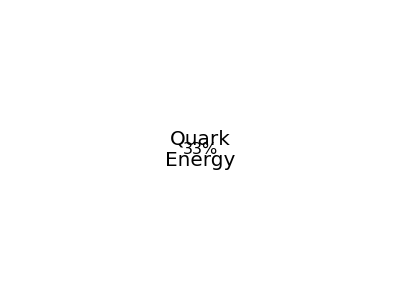
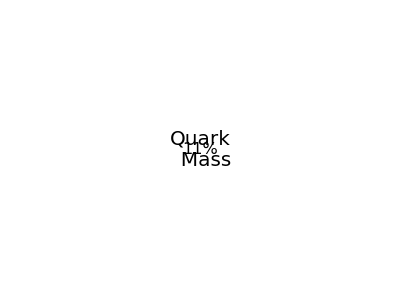
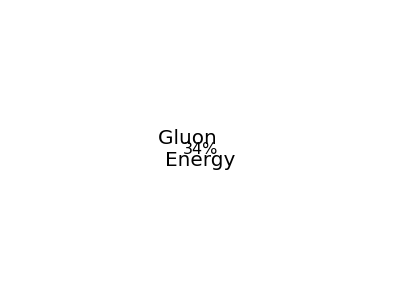
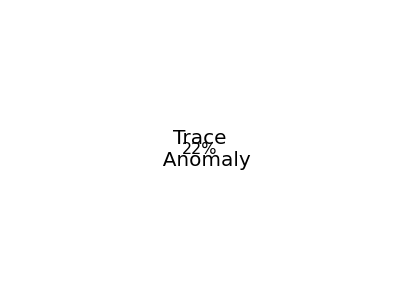

```mathematica
labels={Graphics[{Text[Style["\nQuark\nEnergy\n",20]],Text[Style["\n\n\n\n33%",16]]}],
Graphics[{Text[Style["  Quark\n  Mass\n",20]],Text[Style["\n\n  11%",16]]}],
Graphics[{Text[Style["Gluon    \nEnergy    \n",20]],Text[Style["\n\n\n34%     ",16]]}],
Graphics[{Text[Style["  Trace\n  Anomaly\n",20]],Text[Style["\n\n\n  22%",16]]}]}
```

```mathematica
massbudget=PieChart[{0.324584,0.113221,0.3405,0.221695},
ChartLabels->Placed[labels,"RadialCenter"]]
```

-Graphics-
-Graphics-

```mathematica
Export["/Users/user/Documents/mass.eps",massbudget]
```

/Users/user/Documents/mass.eps

```mathematica
{C1,C2,C3,C4,C5}/.{a->0.654498,b->0,A1->-0.02246,A2->0,A3->0,A4->0,A5->0,ω1->0,ω2->0}
```

{-0.02246,-0.00436145,0.00436145,-0.00549749,0.00549749}

```mathematica
Simplify[N[C1/.{a->1.4,b->0.0,ω1->0,ω2->0}]]
```

1. A1+0.0961729 A2-0.0961729 A3+0.565833 A4-0.565833 A5

```mathematica
Simplify[N[C2/.{a->1.4,b->0.0,ω1->0,ω2->0}]]
```

0.+0.0961729 A1+1. A2-0.0906163 A3-0.565833 A4-0.166816 A5

```mathematica
Simplify[N[C3/.{a->1.4,b->0.0,ω1->0,ω2->0}]]
```

0.-0.0961729 A1-0.0906163 A2+1. A3-0.166816 A4-0.565833 A5

```mathematica
Simplify[N[C4/.{a->1.4,b->0.0,ω1->0,ω2->0}]]
```

0.+0.565833 A1-0.565833 A2-0.166816 A3+1. A4+0.0961729 A5

```mathematica
Simplify[N[C5/.{a->1.4,b->0.0,ω1->0,ω2->0}]]
```

0.-0.565833 A1-0.166816 A2-0.565833 A3+0.0961729 A4+1. A5

```mathematica
s1=0.09617;s2=0.565833;s3=0.09062;s4=0.166816;
```

```mathematica
coef=({{1, s1, -s1, s2, -s2}, {s1, 1, -s3, -s2, -s4}, {-s1, -s3, 1, -s4, -s2}, {s2, -s2, -s4, 1, s1}, {-s2, -s4, -s2, s1, 1}})
```

{{1,0.09617,-0.09617,0.565833,-0.565833},{0.09617,1,-0.09062,-0.565833,-0.166816},{-0.09617,-0.09062,1,-0.166816,-0.565833},{0.565833,-0.565833,-0.166816,1,0.09617},{-0.565833,-0.166816,-0.565833,0.09617,1}}

```mathematica
coef.({{-0.006}, {-0.001}, {0.0001}, {0.002}, {0.01}})//TraditionalForm
```

(-0.0106325
-0.00438591
-0.00522432
0.000115853
0.0136976)

```mathematica
A1->-0.006,A2->-0.001,A3->0.0001,A4->0.002,A5->0.01
```

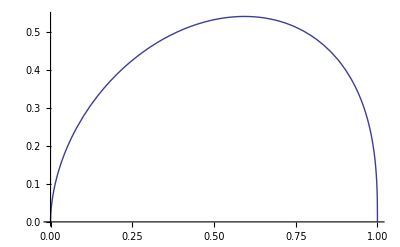

```mathematica
Plot[z^0.54 (1-z)^0.37,{z,0,1}]
```

```mathematica
PP=Integrate[1/(2 Gamma[M/2]) (x/2)^(M/2-1) Exp[-x/2],{x,0,y},Assumptions->{Element[M,Integers],M>0}]
```

1-(M/2y/2)/(M/2)

```mathematica
FindRoot[(PP/.{M->2})==0.683,{y,1}]
```

{y→2.29771}

```mathematica
Print[HoldForm[A==2/(Subscript[P, 1]+Subscript[P, 2])]//TraditionalForm,HoldForm[(√(Subscript[N, 1][Subscript[ϕ, S]]Subscript[N, 2][Subscript[ϕ, S]+π])-√(Subscript[N, 1][Subscript[ϕ, S]+π]Subscript[N, 2][Subscript[ϕ, S]]))/(√(Subscript[N, 1][Subscript[ϕ, S]]Subscript[N, 2][Subscript[ϕ, S]+π])+√(Subscript[N, 1][Subscript[ϕ, S]+π]Subscript[N, 2][Subscript[ϕ, S]]))]//TraditionalForm]
```

A==2/(P_1+P_2)(√(N_1(ϕ_S) N_2(ϕ_S+π))-√(N_1(ϕ_S+π) N_2(ϕ_S)))/(√(N_1(ϕ_S) N_2(ϕ_S+π))+√(N_1(ϕ_S+π) N_2(ϕ_S)))Background→GrayLevel[1]

```mathematica
HoldForm[A==HoldForm[2/(Subscript[P, 1]+Subscript[P, 2])]HoldForm[(√(Subscript[N, 1][Subscript[ϕ, S]]Subscript[N, 2][Subscript[ϕ, S]+π])-√(Subscript[N, 1][Subscript[ϕ, S]+π]Subscript[N, 2][Subscript[ϕ, S]]))/(√(Subscript[N, 1][Subscript[ϕ, S]]Subscript[N, 2][Subscript[ϕ, S]+π])+√(Subscript[N, 1][Subscript[ϕ, S]+π]Subscript[N, 2][Subscript[ϕ, S]]))]]//TraditionalForm
```

A==2/(P_1+P_2) (√(N_1(ϕ_S) N_2(ϕ_S+π))-√(N_1(ϕ_S+π) N_2(ϕ_S)))/(√(N_1(ϕ_S) N_2(ϕ_S+π))+√(N_1(ϕ_S+π) N_2(ϕ_S)))

```mathematica
HoldForm[A^2 P^2]//TraditionalForm
```

A^2 P^2

```mathematica
Subscript[ϕ, h]//TraditionalForm
```

ϕ_h

```mathematica
Subscript[ϕ, S]//TraditionalForm
```

```mathematica
Format[Subscript[F, UU,T],TraditionalForm]:=StyleForm["F_(UU, T)",FontColor->Darker[Black]];
Format[Subscript[F, UU,L],TraditionalForm]:=StyleForm["F_(UU, L)",FontColor->Darker[Black]];
Format[Subscript[F, UUcosϕ],TraditionalForm]:=StyleForm["F_UU^(cos SubscriptBox[ϕ, h])",FontColor->Darker[Black]];
Format[Subscript[F, UUcos2ϕ],TraditionalForm]:=StyleForm["F_UU^(cos 2 SubscriptBox[ϕ, h])",FontColor->Darker[Black]];
Format[Subscript[F, LUsinϕ],TraditionalForm]:=StyleForm["F_LU^(sin SubscriptBox[ϕ, h])",FontColor->Darker[Black]];
Format[Subscript[S, L],TraditionalForm]:=StyleForm["S_L",FontColor->Darker[Blue]];
Format[Subscript[F, ULsinϕ],TraditionalForm]:=StyleForm["F_UL^(sin SubscriptBox[ϕ, h])",FontColor->Darker[Blue]];
Format[Subscript[F, ULsin2ϕ],TraditionalForm]:=StyleForm["F_UL^(sin SubscriptBox[ϕ, h])",FontColor->Darker[Blue]];
Format[Subscript[F, LL],TraditionalForm]:=StyleForm["F_LL",FontColor->Darker[Blue]];
Format[Subscript[F, LLcosϕ],TraditionalForm]:=StyleForm["F_LL^(cos SubscriptBox[ϕ, h])",FontColor->Darker[Blue]];
Format[Subscript[S, T],TraditionalForm]:=StyleForm["S_T",FontColor->Darker[Red]];
Format[Subscript[F, UT,Tsinh$s],TraditionalForm]:=StyleForm["F_(UT, T)^(sin (SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))",FontColor->Darker[Red]];
Format[Subscript[F, UT,Lsinh$s],TraditionalForm]:=StyleForm["F_(UT, L)^(sin (SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))",FontColor->Darker[Red]];
Format[Subscript[F, UTsinhs],TraditionalForm]:=StyleForm["F_UT^(sin (SubscriptBox[ϕ, h] + SubscriptBox[ϕ, S]))",FontColor->Darker[Red]];
Format[Subscript[F, UTsin3h$s],TraditionalForm]:=StyleForm["F_UT^(sin (3 SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))",FontColor->Darker[Red]];
Format[Subscript[F, UTsins],TraditionalForm]:=StyleForm["F_UT^(sin SubscriptBox[ϕ, S])",FontColor->Darker[Red]];
Format[Subscript[F, UTsin2h$s],TraditionalForm]:=StyleForm["F_UT^(sin (2 SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))",FontColor->Darker[Red]];
Format[Subscript[F, LTcosh$s],TraditionalForm]:=StyleForm["F_LT^(cos (SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))",FontColor->Darker[Red]];
Format[Subscript[F, LTcoss],TraditionalForm]:=StyleForm["F_LT^(cos SubscriptBox[ϕ, S])",FontColor->Darker[Red]];
Format[Subscript[F, LTcos2h$s],TraditionalForm]:=StyleForm["F_LT^(cos (2 SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))",FontColor->Darker[Red]];
```

```mathematica
HoldForm[d σ "~"HoldForm[α^2/(x y Q^2)] HoldForm[y^2/(2(1-ϵ))] HoldForm[1+γ^2/(2 x)]]//TraditionalForm
```

d σ ~ α^2/(x y Q^2) y^2/(2 (1-ϵ)) (1+γ^2/(2 x))

```mathematica
HoldForm[d σ "~"HoldForm[α^2/(x y Q^2)] HoldForm[y^2/(2(1-ϵ))] HoldForm[1+γ^2/(2 x)]]//TraditionalForm
HoldForm[
"        {"Subscript[F, UU,T]+ϵ Subscript[F, UU,L]+√(2 ϵ (1+ϵ)) Cos[Subscript[ϕ, h]] Subscript[F, UUcosϕ]"\n       "
+ϵ Cos[2 Subscript[ϕ, h]] Subscript[F, UUcos2ϕ]+Subscript[λ, e] √(2 ϵ (1-ϵ)) Sin[Subscript[ϕ, h]] Subscript[F, LUsinϕ]"\n       "
+Subscript[S, L]"["√(2ϵ (1+ϵ))Sin[Subscript[ϕ, h]] Subscript[F, ULsinϕ]+ϵ Sin[2 Subscript[ϕ, h]] Subscript[F, ULsin2ϕ]"]""\n       "
+Subscript[S, L] Subscript[λ, e]"["√(1-ϵ^2) Subscript[F, LL]+√(2ϵ (1-ϵ)) Cos[Subscript[ϕ, h]] Subscript[F, LLcosϕ]"]""\n       "
+Subscript[S, T] "["Sin[Subscript[ϕ, h]-Subscript[ϕ, S]] "("Subscript[F, UT,Tsinh$s]+ϵ Subscript[F, UT,Lsinh$s]")"+ϵ Sin[Subscript[ϕ, h]+Subscript[ϕ, S]] Subscript[F, UTsinhs]+ϵ Sin[3 Subscript[ϕ, h]-Subscript[ϕ, S]] Subscript[F, UTsin3h$s]"\n       "
+√(2ϵ (1+ϵ)) Sin[Subscript[ϕ, S]] Subscript[F, UTsins]+√(2ϵ (1+ϵ)) Sin[2 Subscript[ϕ, h]-Subscript[ϕ, S]] Subscript[F, UTsin2h$s]"]""\n       "
+Subscript[S, T] Subscript[λ, e]"["√(1-ϵ^2) Cos[Subscript[ϕ, h]-Subscript[ϕ, S]] Subscript[F, LTcosh$s]+√(2ϵ(1-ϵ)) Cos[Subscript[ϕ, S]] Subscript[F, LTcoss]+√(2ϵ(1-ϵ))Cos[2 Subscript[ϕ, h]-Subscript[ϕ, S]] Subscript[F, LTcos2h$s]"]}"]//TraditionalForm
```

d σ ~ α^2/(x y Q^2) y^2/(2 (1-ϵ)) (1+γ^2/(2 x))

{ F_(UU, T)+ϵ F_(UU, L)+√(2 ϵ (1+ϵ)) cos(ϕ_h) F_UU^(cos SubscriptBox[ϕ, h]) 
       +ϵ cos(2 ϕ_h) F_UU^(cos 2 SubscriptBox[ϕ, h])+λ_e √(2 ϵ (1-ϵ)) sin(ϕ_h) F_LU^(sin SubscriptBox[ϕ, h]) 
       +S_L [ √(2 ϵ (1+ϵ)) sin(ϕ_h) F_UL^(sin SubscriptBox[ϕ, h])+ϵ sin(2 ϕ_h) F_UL^(sin SubscriptBox[ϕ, h]) ] 
       +S_L λ_e [ √(1-ϵ^2) F_LL+√(2 ϵ (1-ϵ)) cos(ϕ_h) F_LL^(cos SubscriptBox[ϕ, h]) ] 
       +S_T [ sin(ϕ_h-ϕ_S) ( F_(UT, T)^(sin (SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))+ϵ F_(UT, L)^(sin (SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S])) )+ϵ sin(ϕ_h+ϕ_S) F_UT^(sin (SubscriptBox[ϕ, h] + SubscriptBox[ϕ, S]))+ϵ sin(3 ϕ_h-ϕ_S) F_UT^(sin (3 SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S])) 
       +√(2 ϵ (1+ϵ)) sin(ϕ_S) F_UT^(sin SubscriptBox[ϕ, S])+√(2 ϵ (1+ϵ)) sin(2 ϕ_h-ϕ_S) F_UT^(sin (2 SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S])) ] 
       +S_T λ_e [ √(1-ϵ^2) cos(ϕ_h-ϕ_S) F_LT^(cos (SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S]))+√(2 ϵ (1-ϵ)) cos(ϕ_S) F_LT^(cos SubscriptBox[ϕ, S])+√(2 ϵ (1-ϵ)) cos(2 ϕ_h-ϕ_S) F_LT^(cos (2 SubscriptBox[ϕ, h] - SubscriptBox[ϕ, S])) ]}

```mathematica
Format[FF,TraditionalForm]:=StyleForm["F^",FontColor->Darker[Blue]];
Format[x,TraditionalForm]:=StyleForm["x_",FontColor->Blue];
Format[z,TraditionalForm]:=StyleForm["z_",FontColor->Red];
Format[Pt,TraditionalForm]:=StyleForm["P_T",FontColor->Darker[Green]];
Format[Q2,TraditionalForm]:=StyleForm["Q^2",FontColor->Purple];
Format[pt,TraditionalForm]:=StyleForm["p_⊥",Darker[Blue]];
```

```mathematica
HoldForm[FF"("x","z","Pt","Q2")"=="∑_q e_q^2"x"∫^ "d^2 kt d^2 pt δ^(2)(Pt-pt-z kt)w[kt,pt]f[x,kt,Q2]"D^"[z,pt,Q2]]//TraditionalForm
```

F^ ( x_ , z_ , P_T , Q^2 )==∑_q e_q^2 x_ ∫^  d^2 k_⊥ d^2 p_⊥ δ^2 (P_T-p_⊥-z_ k_⊥) w(k_⊥,p_⊥) f(x_,k_⊥,Q^2) D^(z_,p_⊥,Q^2)

```mathematica
Clear[x,z]
```

```mathematica
Format[kt,TraditionalForm]:=StyleForm["k_⊥",FontColor->Darker[Blue]]
Format[kt2,TraditionalForm]:=StyleForm["<k_⊥^2>",FontColor->Darker[Black]]
Format[pt,TraditionalForm]:=StyleForm["p_⊥",FontColor->Darker[Blue]]
Format[pt2,TraditionalForm]:=StyleForm["<p_⊥^2>",FontColor->Darker[Black]]
```

```mathematica
HoldForm[f[x,kt,Q^2]==f[x,Q^2] HoldForm[(E^(-kt^2/kt2))/(π kt2)]]//TraditionalForm
```

f(x,k_⊥,Q^2)==f(x,Q^2) (exp(-(k_⊥)^2/(<k_⊥^2>)))/(π <k_⊥^2>)

```mathematica
HoldForm["D_"[z,pt,Q^2]=="D_"[z,Q^2] HoldForm[(E^(-pt^2/pt2))/(π pt2)]]//TraditionalForm
```

D_(z,p_⊥,Q^2)==D_(z,Q^2) (exp(-(p_⊥)^2/(<p_⊥^2>)))/(π <p_⊥^2>)

```mathematica
Clear[x,kt,pt]
```

```mathematica
Format[NN,TraditionalForm]:=StyleForm["N_",FontColor->Blue]
Format[kt,TraditionalForm]:=StyleForm["k_⊥",FontColor->Black]
Format[α,TraditionalForm]:=StyleForm["α",FontColor->Blue]
Format[β,TraditionalForm]:=StyleForm["β",FontColor->Blue]
Format[M1,TraditionalForm]:=StyleForm["M_T",FontColor->Blue]
Format[K2,TraditionalForm]:=StyleForm["K^2",FontColor->Black]
Format[f1T,TraditionalForm]:=StyleForm["f_(1  T)^⊥",FontColor->Black]
Format[h1T,TraditionalForm]:=StyleForm["h_(1  T)^⊥",FontColor->Black]
```

```mathematica
HoldForm[f1T[x,kt,Q^2]==-NN Subscript[f, 1][x,Q^2] x^α (1-x)^β √(2 E) HoldForm[(α+β)^(α+β)/(α^α β^β)]HoldForm[(M1 Subscript[M, p])/(M1^2+kt2)]HoldForm[Exp[-kt^2/K2]/(π K2)]]//TraditionalForm
```

f_(1  T)^⊥(x,k_⊥,Q^2)==-N_ f_1(x,Q^2) x^α (1-x)^β √(2 ⅇ) (α+β)^(α+β)/(α^α β^β) (M_S M_p)/(M_S^2+<k_⊥^2>) (exp(-(k_⊥)^2/K^2))/(π K^2)

```mathematica
HoldForm[K2==HoldForm[(M1^2 kt2)/(M1^2+kt2)]]//TraditionalForm
```

K^2==(M_S^2 <k_⊥^2>)/(M_S^2+<k_⊥^2>)

```mathematica
HoldForm[Subscript[h, 1][x,kt,Q^2]==HoldForm[NN/2] (Subscript[f, 1][x,Q^2]+Subscript[g, 1][x,Q^2])  x^α (1-x)^β HoldForm[(α+β)^(α+β)/(α^α β^β)]HoldForm[Exp[-kt^2/kt2]/(π kt2)]]//TraditionalForm
```

h_1(x,k_⊥,Q^2)==N_/2 (f_1(x,Q^2)+g_1(x,Q^2)) x^α (1-x)^β (α+β)^(α+β)/(α^α β^β) (exp(-(k_⊥)^2/(<k_⊥^2>)))/(π <k_⊥^2>)

```mathematica
HoldForm[h1T[x,kt,Q^2]==NN (Subscript[f, 1][x,Q^2]-Subscript[g, 1][x,Q^2]) x^α (1-x)^β E HoldForm[(α+β)^(α+β)/(α^α β^β)]HoldForm[Subscript[M, p]^2/(M1^2+kt2)]HoldForm[Exp[-kt^2/K2]/(π K2)]]//TraditionalForm
```

h_(1  T)^⊥(x,k_⊥,Q^2)==N_ (f_1(x,Q^2)-g_1(x,Q^2)) x^α (1-x)^β ⅇ (α+β)^(α+β)/(α^α β^β) M_p^2/(M_T^2+<k_⊥^2>) (exp(-(k_⊥)^2/K^2))/(π K^2)

```mathematica
Format[kt,TraditionalForm]:=StyleForm["k_⊥",FontColor->Darker[Blue]]
```

```mathematica
HoldForm[K2==HoldForm[(M1^2 kt2)/(M1^2+kt2)]]//TraditionalForm
```

K^2==(M_T^2 <k_⊥^2>)/(M_T^2+<k_⊥^2>)

```mathematica
HoldForm[Subscript[L, z]==-"∫"d x d^2 kt HoldForm[kt^2/(2 Subscript[M, p]^2)] h1T[x,kt^2]]//TraditionalForm
```

L_z==-∫ d x d^2 k_⊥ (k_⊥)^2/(2 M_p^2) h_(1  T)^⊥(x,(k_⊥)^2)

```mathematica
Format[Lx,TraditionalForm]:=StyleForm["L_(\n)(x)",FontColor->Darker[Red]]
```

```mathematica
HoldForm["f_(1  T)^(⊥(0))""("x","Subscript[Q, 0]^2")"==-Lx "E_"[x,0,0,Subscript[Q, 0]^2]]//TraditionalForm
```

f_(1  T)^(⊥(0)) ( x , Q_0^2 )==-L_(\n)(x) E_(x,0,0,Q_0^2)

```mathematica
HoldForm[Lx==HoldForm[("K")/(1-x)^η]]//TraditionalForm
```

L_(\n)(x)==K/(1-x)^η

```mathematica
HoldForm["J^"==HoldForm[1/2]"∫"d x x"["H[x,0,0]+"E^"[x,0,0]"]"]//TraditionalForm
```

J^==1/2 ∫ d x x [ H(x,0,0)+E^(x,0,0) ]

```mathematica
HoldForm["A_UT"==HoldForm[(ϵ Subscript[F, UT][x,z,Subscript[P, T],Q^2])/(Subscript[F, UU,T][x,z,Subscript[P, T],Q^2])]]//TraditionalForm
```

A_UT==(ϵ F_UT(x,z,P_T,Q^2))/(F_(UU,T)(x,z,P_T,Q^2))

```mathematica
HoldForm[ϵ==HoldForm[(1-y-HoldForm[1/4] γ^2 y^2)/(1-y+HoldForm[1/2] y^2+HoldForm[1/4] γ^2 y^2)]]//TraditionalForm
```

ϵ==(1-y-1/4 γ^2 y^2)/(1-y+1/2 y^2+1/4 γ^2 y^2)

## Uncertainties

```mathematica
σ[ϕh_,ϕS_]:=A1 Sin[ϕh-ϕS]+A2 Sin[ϕh+ϕS]+A3 Sin[3 ϕh-ϕS];
```

```mathematica
{Integrate[σ[ϕh,ϕS] Sin[ϕh-ϕS],{ϕS,0,π},{ϕh,-π,π}],
Integrate[σ[ϕh,ϕS] Sin[ϕh+ϕS],{ϕS,0,π},{ϕh,-π,π}],
Integrate[σ[ϕh,ϕS] Sin[3 ϕh-ϕS],{ϕS,0,π},{ϕh,-π,π}]}//TraditionalForm
```

{π^2 A_1,π^2 A_2,π^2 A_3}

```mathematica
{I1=Integrate[σ[ϕh,ϕS] Sin[ϕh-ϕS],{ϕS,0,π},{ϕh,-b,-a}]+Integrate[σ[ϕh,ϕS] Sin[ϕh-ϕS],{ϕS,0,π},{ϕh,a,b}],
I2=Integrate[σ[ϕh,ϕS] Sin[ϕh+ϕS],{ϕS,0,π},{ϕh,-b,-a}]+Integrate[σ[ϕh,ϕS] Sin[ϕh+ϕS],{ϕS,0,π},{ϕh,a,b}],
I3=Integrate[σ[ϕh,ϕS] Sin[3 ϕh-ϕS],{ϕS,0,π},{ϕh,-b,-a}]+Integrate[σ[ϕh,ϕS] Sin[3 ϕh-ϕS],{ϕS,0,π},{ϕh,a,b}]}//TraditionalForm
```

{1/2 π (2 A_1 (b-a)+(A_2-A_3) (sin(2 a)-sin(2 b))),-1/4 π (-2 A_1 sin(2 a)+4 a A_2-A_3 sin(4 a)+2 A_1 sin(2 b)-4 b A_2+A_3 sin(4 b)),-1/4 π (2 A_1 sin(2 a)-A_2 sin(4 a)+4 a A_3-2 A_1 sin(2 b)+A_2 sin(4 b)-4 b A_3)}

```mathematica
Mc={{Coefficient[I1,A1],Coefficient[I1,A2],Coefficient[I1,A3]},
{Coefficient[I2,A1],Coefficient[I2,A2],Coefficient[I2,A3]},
{Coefficient[I3,A1],Coefficient[I3,A2],Coefficient[I3,A3]}}//TraditionalForm
```

((b-a) π | 1/2 π (sin(2 a)-sin(2 b)) | 1/2 π (sin(2 b)-sin(2 a))
-1/4 π (2 sin(2 b)-2 sin(2 a)) | -1/4 (4 a-4 b) π | -1/4 π (sin(4 b)-sin(4 a))
-1/4 π (2 sin(2 a)-2 sin(2 b)) | -1/4 π (sin(4 b)-sin(4 a)) | -1/4 (4 a-4 b) π)

### Statistics

```mathematica
Format[M1,TraditionalForm]:=Style["M_1",FontColor->Blue];
Format[M2,TraditionalForm]:=Style["M_2",FontColor->Blue];
Format[M3,TraditionalForm]:=Style["M_3",FontColor->Blue];
```

```mathematica
Integrate[(M1 Sin[ϕh-ϕS]+M2 Sin[ϕh+ϕS]+M3 Sin[3ϕh-ϕS])^2,{ϕS,0,π},{ϕh,-b,-a}]+Integrate[(M1 Sin[ϕh-ϕS]+M2 Sin[ϕh+ϕS]+M3 Sin[3ϕh-ϕS])^2,{ϕS,0,π},{ϕh,a,b}]//TraditionalForm
```

1/2 π (-2 (a-b) (M_1^2+M_2^2+M_3^2)+4 M_1 (M_2-M_3) sin(a-b) cos(a+b)+M_2 M_3 (sin(4 a)-sin(4 b)))

```mathematica
D[σ[ϕh,ϕS],ϕh]//TraditionalForm
```

A_1 cos(ϕ_h-ϕ_S)+A_2 cos(ϕ_h+ϕ_S)+3 A_3 cos(3 ϕ_h-ϕ_S)

```mathematica
Integrate[(kt^2/(2 M^2))^n Exp[-kt^2/Kt^2]/(π Kt^2) 2 π kt,{kt,0,Infinity},Assumptions->{Kt>0,Element[n,Integers],n≥0}]
```

2^-n Kt^(2 n) M^(-2 n) Gamma[1+n]

```mathematica
D[σ[ϕh,ϕS],ϕh]//TraditionalForm
```

A_1 cos(ϕ_h-ϕ_S)+A_2 cos(ϕ_h+ϕ_S)+3 A_3 cos(3 ϕ_h-ϕ_S)

```mathematica
D[σ[ϕh,ϕS],ϕS]//TraditionalForm
```

-A_1 cos(ϕ_h-ϕ_S)+A_2 cos(ϕ_h+ϕ_S)-A_3 cos(3 ϕ_h-ϕ_S)

```mathematica
MS[ϕh_,ϕS_]:={{Sin[ϕh-ϕS]^2,Sin[ϕh-ϕS] Sin[ϕh+ϕS],Sin[ϕh-ϕS] Sin[3 ϕh-ϕS]},{Sin[ϕh+ϕS] Sin[ϕh-ϕS],Sin[ϕh+ϕS]^2,Sin[ϕh+ϕS] Sin[3 ϕh-ϕS]},{Sin[3 ϕh-ϕS] Sin[ϕh-ϕS],Sin[3 ϕh-ϕS] Sin[ϕh+ϕS],Sin[3 ϕh-ϕS]^2}};
```

```mathematica
Integrate[MS[ϕh,ϕS],{ϕS,0,π}]//TraditionalForm
```

(π/2 | -1/2 π cos(2 ϕh) | 1/2 π cos(2 ϕh)
-1/2 π cos(2 ϕh) | π/2 | -1/2 π cos(4 ϕh)
1/2 π cos(2 ϕh) | -1/2 π cos(4 ϕh) | π/2)

```mathematica
Integrate[%,{ϕh,-π,π}]
```

(π^2 | 0 | 0
0 | π^2 | 0
0 | 0 | π^2)

```mathematica
Integrate[(A1 Sin[ϕh-ϕS]+A2 Sin[ϕh+ϕS]+A3 Sin[3 ϕh-ϕS])^2,{ϕS,0,π},{ϕh,0,2π}]
```

(A1^2+A2^2+A3^2) π^2

```mathematica
0.00086*√3
```

0.00148956

## TMD Plots

```mathematica
VerticleLines=Graphics[{{Dashed,Line[{{0.05,-1},{0.05,1}}]},{Dashed,Line[{{0.6,-1},{0.6,1}}]}}];
leg=Graphics[{{Lighter[Gray,0.5],Rectangle[{0,0},{2,1}]},{Darker[Red,0.07],Rectangle[{0,-1.5},{2,-0.5}]}}];
```

```mathematica
Export["/Users/user/Documents/SoLID/leg.eps",leg]
```

/Users/user/Documents/SoLID/leg.eps

### Sivers

```mathematica
datalist={{0.010000,-0.005526,-0.004978,-0.006100,0.004311,0.004679,0.003972},{0.030000,-0.014200,-0.013371,-0.015008,0.014631,0.015249,0.014006},{0.050000,-0.021891,-0.021005,-0.022733,0.025375,0.026017,0.024689},{0.070000,-0.028438,-0.027601,-0.029211,0.035343,0.035943,0.034725},{0.090000,-0.033788,-0.033052,-0.034443,0.043898,0.044398,0.043408},{0.110000,-0.037955,-0.037296,-0.038568,0.050714,0.051172,0.050276},{0.130000,-0.040988,-0.040424,-0.041597,0.055672,0.056158,0.055220},{0.150000,-0.042955,-0.042417,-0.043537,0.058796,0.059293,0.058316},{0.170000,-0.043939,-0.043406,-0.044476,0.060208,0.060727,0.059696},{0.190000,-0.044035,-0.043524,-0.044528,0.060094,0.060617,0.059559},{0.210000,-0.043348,-0.042874,-0.043831,0.058679,0.059186,0.058139},{0.230000,-0.041991,-0.041517,-0.042488,0.056199,0.056679,0.055682},{0.250000,-0.040077,-0.039587,-0.040598,0.052897,0.053352,0.052406},{0.270000,-0.037723,-0.037181,-0.038254,0.048999,0.049488,0.048511},{0.290000,-0.035039,-0.034460,-0.035569,0.044718,0.045235,0.044234},{0.310000,-0.032134,-0.031532,-0.032652,0.040239,0.040775,0.039770},{0.330000,-0.029104,-0.028495,-0.029661,0.035728,0.036269,0.035239},{0.350000,-0.026038,-0.025435,-0.026637,0.031312,0.031860,0.030797},{0.370000,-0.023013,-0.022427,-0.023637,0.027100,0.027670,0.026573},{0.390000,-0.020092,-0.019514,-0.020724,0.023166,0.023742,0.022618},{0.410000,-0.017328,-0.016767,-0.017952,0.019563,0.020129,0.019011},{0.430000,-0.014759,-0.014225,-0.015363,0.016320,0.016863,0.015781},{0.450000,-0.012414,-0.011915,-0.012984,0.013447,0.013957,0.012934},{0.470000,-0.010307,-0.009851,-0.010837,0.010941,0.011410,0.010465},{0.490000,-0.008445,-0.008035,-0.008927,0.008786,0.009209,0.008354},{0.510000,-0.006826,-0.006463,-0.007257,0.006961,0.007335,0.006577},{0.530000,-0.005439,-0.005124,-0.005817,0.005439,0.005763,0.005103},{0.550000,-0.004270,-0.004001,-0.004595,0.004188,0.004464,0.003901},{0.570000,-0.003299,-0.003070,-0.003574,0.003176,0.003407,0.002936},{0.590000,-0.002507,-0.002316,-0.002735,0.002370,0.002560,0.002174},{0.610000,-0.001871,-0.001715,-0.002057,0.001740,0.001894,0.001582},{0.630000,-0.001370,-0.001245,-0.001518,0.001256,0.001379,0.001131},{0.650000,-0.000982,-0.000885,-0.001097,0.000890,0.000986,0.000793},{0.670000,-0.000688,-0.000613,-0.000776,0.000618,0.000692,0.000545},{0.690000,-0.000470,-0.000415,-0.000535,0.000420,0.000476,0.000367},{0.710000,-0.000312,-0.000272,-0.000360,0.000279,0.000320,0.000241},{0.730000,-0.000201,-0.000173,-0.000235,0.000181,0.000210,0.000154},{0.750000,-0.000125,-0.000106,-0.000148,0.000114,0.000135,0.000096},{0.770000,-0.000075,-0.000062,-0.000089,0.000070,0.000084,0.000058},{0.790000,-0.000042,-0.000035,-0.000052,0.000041,0.000050,0.000034},{0.810000,-0.000023,-0.000018,-0.000028,0.000023,0.000029,0.000019},{0.830000,-0.000011,-0.000009,-0.000014,0.000013,0.000016,0.000010},{0.850000,-0.000005,-0.000004,-0.000007,0.000006,0.000008,0.000005},{0.870000,-0.000002,-0.000002,-0.000003,0.000003,0.000004,0.000002},{0.890000,-0.000001,-0.000001,-0.000001,0.000001,0.000002,0.000001},{0.910000,-0.000000,-0.000000,-0.000000,0.000000,0.000001,0.000000},{0.930000,-0.000000,-0.000000,-0.000000,0.000000,0.000000,0.000000},{0.950000,-0.000000,-0.000000,-0.000000,0.000000,0.000000,0.000000},{0.970000,-0.000000,-0.000000,-0.000000,0.000000,0.000000,0.000000},{0.990000,-0.000000,-0.000000,-0.000000,0.000000,0.000000,0.000000}};
ulistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{2}],2];
ulistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{3}],2];
ulistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{4}],2];
dlistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{5}],2];
dlistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{6}],2];
dlistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{7}],2];
```

```mathematica
uoldlist={{0.001000000000000002,0.0128898128898129,0.001372141372141378,0.,0.00108737},{0.0013325451527579557,0.013222453222453237,0.0017047817047816918,0.,0.00129579},{0.001770482355847965,0.013762993762993758,0.0020374220374220296,0.0003326403326403376,0.00155047},{0.0031346077723689567,0.014885654885654902,0.003035343035343042,0.00045738045738044354,0.0022773},{0.004177006392867658,0.015467775467775474,0.0037006237006236937,0.0005405405405405456,0.00279724},{0.005566049621854773,0.016257796257796255,0.004490644490644498,0.0008731808731808596,0.00346757},{0.007395316118836327,0.01692307692307693,0.005530145530145539,0.0013305613305613269,0.00432752},{0.009768365091638323,0.017588357588357605,0.006777546777546787,0.0019126819126819,0.0054205},{0.013016787553232635,0.018503118503118515,0.008357588357588349,0.002744282744282732,0.00689184},{0.017498569409979497,0.019501039501039506,0.010145530145530143,0.0042827442827442904,0.00888045},{0.023113604858983446,0.020997920997921013,0.012390852390852405,0.00619542619542619,0.0113111},{0.03053042320548472,0.022661122661122676,0.015218295218295215,0.008773388773388766,0.0144171},{0.040564160614000845,0.024823284823284837,0.018503118503118515,0.012182952182952197,0.0183967},{0.05453071867070408,0.027318087318087332,0.022785862785862806,0.017130977130977137,0.0234779},{0.07202883015752326,0.031018711018711027,0.02752598752598754,0.02291060291060291,0.0290353},{0.09598166848523342,0.036424116424116436,0.03284823284823287,0.027983367983368007,0.0351559},{0.1161142432724506,0.040623700623700645,0.03609147609147612,0.030478170478170506,0.0389976},{0.12752577290626452,0.04266112266112268,0.03767151767151768,0.03180873180873183,0.040669},{0.14506999902916534,0.04444906444906447,0.0393762993762994,0.03214137214137217,0.0425675},{0.16993385053795423,0.04681912681912684,0.04074844074844078,0.032390852390852404,0.0439361},{0.18554439397901581,0.04669438669438673,0.04083160083160085,0.03089397089397092,0.0440851},{0.22644452882384528,0.04582120582120585,0.03950103950103953,0.027858627858627878,0.0422799},{0.24869914960301237,0.04469854469854473,0.03758835758835761,0.02436590436590437,0.0402165},{0.28962234198427994,0.04253638253638257,0.03318087318087321,0.018711018711018726,0.0350956},{0.3008648840387527,0.04174636174636177,0.03180873180873183,0.017380457380457397,0.033477},{0.32850307576635046,0.038253638253638284,0.02752598752598754,0.013762993762993758,0.0293336},{0.3792105463352715,0.03214137214137217,0.020623700623700624,0.007983367983367984,0.021653},{0.4009160428609234,0.0296881496881497,0.018045738045738047,0.0057380457380457470,0.0185635},{0.43391491671849874,0.026070686070686085,0.014220374220374225,0.004158004158004161,0.0142838},{0.5097757060954785,0.01783783783783784,0.007110187110187101,0.0012474012474012483,0.00684085},{0.5517346761108954,0.014095634095634095,0.0046153846153846045,0.00045738045738044354,0.0041797},{0.6113072436739222,0.009812889812889806,0.0022453222453222375,0.0003326403326403376,0.00183486},{0.7118972295136942,0.0037006237006236937,0.00045738045738044354,0.,0.000300038},{1.,0.,0.,0.,0.}};
uoldupper=Join[Take[uoldlist,All,{1}],-(Take[uoldlist,All,{2}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}]),2];
uoldcenter=Join[Take[uoldlist,All,{1}],-Take[uoldlist,All,{5}],2];
uoldlower=Join[Take[uoldlist,All,{1}],-(Take[uoldlist,All,{4}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}]),2];
```

```mathematica
doldlist={{0.001000000000000002,0.,-0.00044444444444444447,-0.006400000000000015,-0.000424231},{0.0013325451527579557,0.,-0.0007111111111111212,-0.0071111111111111115,-0.000555255},{0.001770482355847965,0.,-0.0009333333333333435,-0.007955555555555572,-0.000727606},{0.0031346077723689567,-0.00022222222222222223,-0.0015555555555555557,-0.01035555555555556,-0.00127608},{0.004177006392867658,-0.0003555555555555606,-0.0020444444444444546,-0.011555555555555557,-0.00170755},{0.005566049621854773,-0.00044444444444444447,-0.0027555555555555506,-0.013111111111111112,-0.00230036},{0.007395316118836327,-0.0007111111111111212,-0.0038222222222222325,-0.014933333333333344,-0.00310949},{0.009768365091638323,-0.001066666666666682,-0.005288888888888905,-0.016755555555555565,-0.00420174},{0.013016787553232635,-0.001688888888888894,-0.006755555555555551,-0.01902222222222223,-0.00576407},{0.017498569409979497,-0.002888888888888889,-0.008888888888888889,-0.021688888888888896,-0.0080129},{0.023113604858983446,-0.004577777777777783,-0.011822222222222232,-0.024577777777777785,-0.0109393},{0.03053042320548472,-0.007466666666666672,-0.015644444444444454,-0.02795555555555556,-0.0149178},{0.040564160614000845,-0.011822222222222232,-0.02071111111111112,-0.03182222222222223,-0.020346},{0.05453071867070408,-0.017733333333333337,-0.02702222222222223,-0.0364,-0.0277304},{0.07202883015752326,-0.023866666666666675,-0.03497777777777779,-0.0420888888888889,-0.036283},{0.09598166848523342,-0.028444444444444446,-0.04377777777777778,-0.05413333333333334,-0.0461268},{0.1161142432724506,-0.030755555555555564,-0.04946666666666667,-0.061511111111111114,-0.0524242},{0.12752577290626452,-0.031955555555555556,-0.0520888888888889,-0.06511111111111112,-0.0551543},{0.14506999902916534,-0.032177777777777784,-0.054622222222222225,-0.06720000000000001,-0.0581947},{0.16993385053795423,-0.03231111111111112,-0.05666666666666667,-0.06911111111111111,-0.0602046},{0.18554439397901581,-0.030977777777777788,-0.05657777777777778,-0.06804444444444446,-0.0602417},{0.22644452882384528,-0.027733333333333336,-0.05355555555555556,-0.06453333333333335,-0.0567136},{0.24869914960301237,-0.023866666666666675,-0.04991111111111112,-0.060044444444444456,-0.053132},{0.28962234198427994,-0.01760000000000001,-0.042577777777777784,-0.05328888888888889,-0.0448057},{0.3008648840387527,-0.01613333333333334,-0.040400000000000005,-0.051155555555555565,-0.0422908},{0.32850307576635046,-0.012755555555555551,-0.03484444444444445,-0.04524444444444445,-0.0360642},{0.3792105463352715,-0.007466666666666672,-0.02506666666666667,-0.035911111111111116,-0.0252519},{0.4009160428609234,-0.005422222222222217,-0.021466666666666672,-0.03244444444444445,-0.0211592},{0.43391491671849874,-0.003955555555555571,-0.01688888888888889,-0.02688888888888889,-0.0157306},{0.5097757060954785,-0.001288888888888904,-0.007333333333333334,-0.01724444444444445,-0.00697819},{0.5517346761108954,-0.00044444444444444447,-0.0044444444444444444,-0.012755555555555551,-0.00409268},{0.6113072436739222,-0.0003555555555555606,-0.0021333333333333386,-0.008444444444444445,-0.00170469},{0.7118972295136942,-0.00008888888888888384,-0.0003555555555555606,-0.002266666666666677,-0.000268503},{1.,0.,0.,0.,0.}};
doldupper=Join[Take[doldlist,All,{1}],-(Take[doldlist,All,{2}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}]),2];
doldcenter=Join[Take[doldlist,All,{1}],-Take[doldlist,All,{5}],2];
doldlower=Join[Take[doldlist,All,{1}],-(Take[doldlist,All,{4}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}]),2];
```

```mathematica
uold=ListPlot[{uoldupper,uoldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.072,0.002}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xf_(1  T)^(⊥(1) u)",18]},LabelStyle->14];
```

```mathematica
unew=ListPlot[{ulistcenter,ulistupper,ulistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.072,0.002}},PlotStyle->{{Black,Thickness[0.003]},None,None}];
```

```mathematica
dold=ListPlot[{doldupper,doldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.002,0.082}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xf_(1  T)^(⊥(1) d)",18]},LabelStyle->14];
```

```mathematica
dnew=ListPlot[{dlistcenter,dlistupper,dlistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.002,0.082}},PlotStyle->{{Black,Thickness[0.003]},None,None}];
```

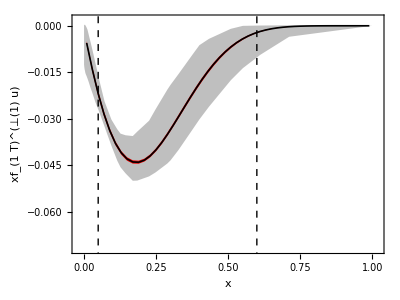

```mathematica
plotf1tMu=Show[uold,unew,VerticleLines]
```

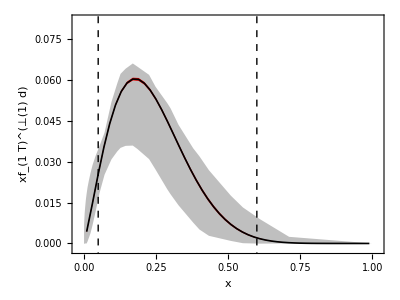

```mathematica
plotf1tMd=Show[dold,dnew,VerticleLines]
```

```mathematica
Export["/Users/user/Documents/SoLID/lsivers_u.eps",plotf1tMu];
Export["/Users/user/Documents/SoLID/lsivers_d.eps",plotf1tMd];
```

### Sivers kt

```mathematica
datalist={{0.000000,-0.000000,-0.000000,-0.000000,0.000000,0.000000,0.000000},{0.020000,-0.041346,-0.038257,-0.044778,0.054568,0.058479,0.050884},{0.040000,-0.082006,-0.075901,-0.088789,0.108230,0.115953,0.100954},{0.060000,-0.121313,-0.112338,-0.131289,0.160107,0.171445,0.149417},{0.080000,-0.158637,-0.147003,-0.171575,0.209367,0.224036,0.195524},{0.100000,-0.193402,-0.179379,-0.209007,0.255250,0.272887,0.238586},{0.120000,-0.225102,-0.209008,-0.243034,0.297087,0.317264,0.277994},{0.140000,-0.253309,-0.235501,-0.273185,0.334314,0.356554,0.313232},{0.160000,-0.277687,-0.258549,-0.299093,0.366488,0.390280,0.343888},{0.180000,-0.297995,-0.277925,-0.320502,0.393290,0.418108,0.369659},{0.200000,-0.314092,-0.293489,-0.337268,0.414534,0.439852,0.390361},{0.220000,-0.325932,-0.305187,-0.349356,0.430161,0.455471,0.405920},{0.240000,-0.333566,-0.313048,-0.356839,0.440237,0.465064,0.416375},{0.260000,-0.337131,-0.317165,-0.359885,0.444942,0.468855,0.421868},{0.280000,-0.336843,-0.317519,-0.358751,0.444561,0.467185,0.422636},{0.300000,-0.332983,-0.314546,-0.353765,0.439467,0.460489,0.418995},{0.320000,-0.325890,-0.308543,-0.345315,0.430105,0.449278,0.411330},{0.340000,-0.315942,-0.299847,-0.333835,0.416977,0.434123,0.400081},{0.360000,-0.303549,-0.288821,-0.319784,0.400620,0.415630,0.385721},{0.380000,-0.289131,-0.275847,-0.303636,0.381592,0.394420,0.368696},{0.400000,-0.273114,-0.261309,-0.285865,0.360453,0.371114,0.349263},{0.420000,-0.255915,-0.245588,-0.266968,0.337754,0.346429,0.328247},{0.440000,-0.237930,-0.229046,-0.247546,0.314017,0.321154,0.306137},{0.460000,-0.219530,-0.212028,-0.227766,0.289733,0.295424,0.283390},{0.480000,-0.201050,-0.194366,-0.207986,0.265343,0.269703,0.260424},{0.500000,-0.182788,-0.176697,-0.188703,0.241242,0.244400,0.237617},{0.520000,-0.165001,-0.159488,-0.170425,0.217766,0.220069,0.215186},{0.540000,-0.147900,-0.142946,-0.152841,0.195197,0.197490,0.192881},{0.560000,-0.131657,-0.127058,-0.136162,0.173759,0.176011,0.171060},{0.580000,-0.116400,-0.111965,-0.120653,0.153623,0.155868,0.150654},{0.600000,-0.102219,-0.097991,-0.106200,0.134908,0.137578,0.131756},{0.620000,-0.089170,-0.085182,-0.092865,0.117686,0.120688,0.114303},{0.640000,-0.077275,-0.073551,-0.080677,0.101987,0.105244,0.098484},{0.660000,-0.066532,-0.063088,-0.069638,0.087808,0.091197,0.084283},{0.680000,-0.056912,-0.053759,-0.059830,0.075112,0.078531,0.071652},{0.700000,-0.048372,-0.045484,-0.051137,0.063841,0.067204,0.060501},{0.720000,-0.040852,-0.038154,-0.043436,0.053916,0.057157,0.050733},{0.740000,-0.034284,-0.031785,-0.036668,0.045247,0.048316,0.042265},{0.760000,-0.028591,-0.026309,-0.030766,0.037735,0.040594,0.034983},{0.780000,-0.023696,-0.021636,-0.025657,0.031273,0.033901,0.028769},{0.800000,-0.019517,-0.017679,-0.021267,0.025758,0.028141,0.023508},{0.820000,-0.015976,-0.014354,-0.017523,0.021085,0.023221,0.019087},{0.840000,-0.012997,-0.011581,-0.014352,0.017153,0.019047,0.015399},{0.860000,-0.010509,-0.009285,-0.011685,0.013870,0.015532,0.012346},{0.880000,-0.008446,-0.007397,-0.009466,0.011147,0.012590,0.009836},{0.900000,-0.006747,-0.005856,-0.007628,0.008904,0.010146,0.007787},{0.920000,-0.005357,-0.004607,-0.006112,0.007070,0.008129,0.006127},{0.940000,-0.004228,-0.003602,-0.004868,0.005580,0.006475,0.004790},{0.960000,-0.003317,-0.002799,-0.003855,0.004377,0.005128,0.003722},{0.980000,-0.002586,-0.002162,-0.003035,0.003413,0.004037,0.002875}};
ulistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{2}],2];
ulistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{3}],2];
ulistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{4}],2];
dlistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{5}],2];
dlistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{6}],2];
dlistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{7}],2];
```

```mathematica
uoldlist={{0.,0.,0.,0.,0.},{0.05167844522968192,0.16511627906976745,0.09573643410852704,0.05581395348837198,0.1052},{0.09231448763250898,0.27790697674418585,0.1662790697674417,0.09806201550387597,0.1804},{0.13295053003533552,0.36705426356589127,0.22635658914728662,0.13488372093023254,0.2439},{0.174911660777385,0.42519379844961214,0.2705426356589146,0.1631782945736434,0.2932},{0.2146643109540634,0.45038759689922453,0.29767441860465105,0.18410852713178286,0.3232},{0.2579505300353358,0.44496124031007733,0.3104651162790697,0.19767441860465107,0.3370},{0.29858657243816233,0.413565891472868,0.3073643410852712,0.20116279069767423,0.3334},{0.3392226148409894,0.3662790697674417,0.2914728682170541,0.19767441860465107,0.3164},{0.38118374558303886,0.30930232558139525,0.2662790697674417,0.1883720930232558,0.2882},{0.4222614840989397,0.263953488372093,0.23449612403100764,0.17248062015503868,0.2539},{0.46289752650176674,0.2220930232558139,0.19883720930232554,0.155813953488372,0.2168},{0.5048586572438162,0.18100775193798438,0.16434108527131766,0.13488372093023254,0.1784},{0.5454946996466433,0.14728682170542629,0.13255813953488363,0.09999999999999999,0.1433},{0.5861307420494698,0.1166666666666667,0.1031007751937985,0.0693798449612402,0.1120},{0.6280918727915192,0.08953488372093028,0.0779069767441861,0.04651162790697672,0.0842},{0.6704946996466431,0.06744186046511616,0.05697674418604644,0.028294573643410884,0.0613},{0.7111307420494701,0.050387596899224785,0.03992248062015506,0.017829457364341165,0.0441},{0.7530918727915196,0.037984496124031035,0.028294573643410884,0.010465116279069719,0.0305},{0.7937279151943462,0.026356589147286853,0.017829457364341165,0.0054263565891471965,0.0208},{0.8343639575971732,0.018992248062015406,0.012790697674418643,0.0019379844961240301,0.0138},{0.9174028268551235,0.008527131782945688,0.004263565891472954,0.,0.0054},{1.,0.003100775193798492,0.0019379844961240301,0.,0.002}};
uoldupper=Join[Take[uoldlist,All,{1}],-(Take[uoldlist,All,{2}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}]),2];
uoldcenter=Join[Take[uoldlist,All,{1}],-Take[uoldlist,All,{5}],2];
uoldlower=Join[Take[uoldlist,All,{1}],-(Take[uoldlist,All,{4}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}]),2];
```

```mathematica
doldlist={{0.,0.,0.,0.,0.},{0.05167844522968192,-0.061697722567287915,-0.12919254658385088,-0.203312629399586,-0.1398},{0.09231448763250898,-0.10890269151138719,-0.22277432712215323,-0.34285714285714286,-0.2381},{0.13295053003533552,-0.14741200828157358,-0.3022774327122153,-0.45424430641821945,-0.3218},{0.174911660777385,-0.1788819875776398,-0.3619047619047619,-0.5250517598343685,-0.3870},{0.2146643109540634,-0.203312629399586,-0.40041407867494827,-0.5565217391304347,-0.4266},{0.2579505300353358,-0.2157349896480332,-0.41697722567287787,-0.5507246376811593,-0.4447},{0.29858657243816233,-0.21904761904761905,-0.41242236024844725,-0.5159420289855072,-0.4400},{0.3392226148409894,-0.2157349896480332,-0.39254658385093166,-0.47536231884057967,-0.4176},{0.38118374558303886,-0.20455486542443063,-0.3573498964803313,-0.4260869565217391,-0.3804},{0.4222614840989397,-0.1875776397515528,-0.31469979296066247,-0.37101449275362325,-0.3351},{0.46289752650176674,-0.16770186335403725,-0.26873706004140785,-0.317184265010352,-0.2862},{0.5048586572438162,-0.14161490683229808,-0.22277432712215323,-0.2674948240165632,-0.2354},{0.5454946996466433,-0.10807453416149077,-0.17763975155279502,-0.22028985507246382,-0.1892},{0.5861307420494698,-0.07412008281573512,-0.13830227743271234,-0.17556935817805383,-0.1478},{0.6280918727915192,-0.049689440993788817,-0.10476190476190479,-0.13706004140786757,-0.1111},{0.6704946996466431,-0.03271221532091111,-0.07660455486542442,-0.10351966873706003,-0.0810},{0.7111307420494701,-0.01904761904761914,-0.05507246376811598,-0.07660455486542442,-0.0582},{0.7530918727915196,-0.011180124223602437,-0.03809523809523804,-0.05631469979296075,-0.0402},{0.7937279151943462,-0.006625258799171936,-0.026086956521739174,-0.040579710144927575,-0.0274},{0.8343639575971732,-0.003312629399585968,-0.01697722567287794,-0.029399585921325144,-0.01818},{0.9174028268551235,-0.0012422360248447674,-0.006625258799171936,-0.01366459627329197,-0.0071},{1.,0.,-0.003312629399585968,-0.006625258799171936,-0.00265}};
doldupper=Join[Take[doldlist,All,{1}],-(Take[doldlist,All,{2}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}]),2];
doldcenter=Join[Take[doldlist,All,{1}],-Take[doldlist,All,{5}],2];
doldlower=Join[Take[doldlist,All,{1}],-(Take[doldlist,All,{4}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}]),2];
```

```mathematica
uold=ListPlot[{uoldupper,uoldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.62,0.02}},PlotStyle->{None,None},FrameLabel->{Style["k_⊥/GeV",18],Style["x(2 SubscriptBox[k, ⊥])/m_pf_(1  T)^(⊥u)",16]},LabelStyle->14];
```

```mathematica
unew=ListPlot[{ulistcenter,ulistupper,ulistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.62,0.02}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

```mathematica
dold=ListPlot[{doldupper,doldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.02,0.62}},PlotStyle->{None,None},FrameLabel->{Style["k_⊥/GeV",18],Style["x(2 SubscriptBox[k, ⊥])/m_pf_(1  T)^(⊥d)",18]},LabelStyle->14];
```

```mathematica
dnew=ListPlot[{dlistcenter,dlistupper,dlistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.02,0.62}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

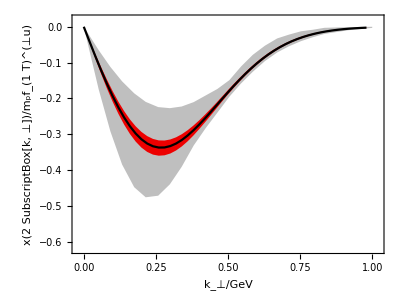

```mathematica
plottmdf1tu=Show[uold,unew]
```

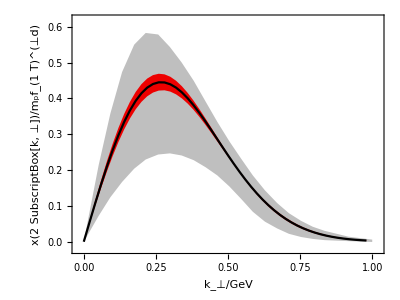

```mathematica
plottmdf1td=Show[dold,dnew]
```

```mathematica
Export["/Users/user/Documents/SoLID/lsivers_kt_u.eps",plottmdf1tu];
Export["/Users/user/Documents/SoLID/lsivers_kt_d.eps",plottmdf1td];
```

### Pretzelosity

```mathematica
datalist={{0.010000,0.000026,0.000138,0.000006,-0.000026,-0.000006,-0.000122},{0.030000,0.000440,0.001463,0.000130,-0.000450,-0.000154,-0.001341},{0.050000,0.001611,0.004276,0.000480,-0.001715,-0.000702,-0.004115},{0.070000,0.003660,0.008382,0.001098,-0.004071,-0.001877,-0.008467},{0.090000,0.006563,0.013462,0.001978,-0.007610,-0.003786,-0.014225},{0.110000,0.010214,0.019184,0.003089,-0.012291,-0.006440,-0.021098},{0.130000,0.014456,0.025233,0.004385,-0.017964,-0.009829,-0.028724},{0.150000,0.019109,0.031326,0.005811,-0.024400,-0.013854,-0.036714},{0.170000,0.023989,0.037224,0.007311,-0.031316,-0.018366,-0.044681},{0.190000,0.028892,0.042696,0.008822,-0.038401,-0.023155,-0.052273},{0.210000,0.033625,0.047556,0.010285,-0.045348,-0.027641,-0.059319},{0.230000,0.038005,0.051648,0.011644,-0.051862,-0.031634,-0.065430},{0.250000,0.041863,0.054847,0.012845,-0.057686,-0.034629,-0.070404},{0.270000,0.045066,0.057084,0.013846,-0.062596,-0.036726,-0.074094},{0.290000,0.047491,0.058639,0.014610,-0.066439,-0.038161,-0.076907},{0.310000,0.049057,0.059216,0.015109,-0.069114,-0.038917,-0.078449},{0.330000,0.049721,0.058756,0.015331,-0.070577,-0.039009,-0.078652},{0.350000,0.049473,0.057306,0.015270,-0.070836,-0.038473,-0.077586},{0.370000,0.048369,0.054981,0.014944,-0.069940,-0.037363,-0.075661},{0.390000,0.046461,0.051940,0.014368,-0.067999,-0.035762,-0.072914},{0.410000,0.043878,0.048375,0.013581,-0.065133,-0.033749,-0.069258},{0.430000,0.040716,0.044300,0.012613,-0.061498,-0.031417,-0.064873},{0.450000,0.037034,0.039789,0.011481,-0.057272,-0.028865,-0.059956},{0.470000,0.033236,0.035280,0.010312,-0.052570,-0.026155,-0.054633},{0.490000,0.029211,0.030702,0.009070,-0.047594,-0.023388,-0.049197},{0.510000,0.025245,0.026301,0.007844,-0.042482,-0.020628,-0.043759},{0.530000,0.021448,0.022157,0.006669,-0.037375,-0.017942,-0.038390},{0.550000,0.017794,0.018282,0.005536,-0.032410,-0.015388,-0.033290},{0.570000,0.014619,0.015046,0.004551,-0.027678,-0.013002,-0.028486},{0.590000,0.011710,0.012147,0.003648,-0.023279,-0.010824,-0.024147},{0.610000,0.009226,0.009650,0.002876,-0.019268,-0.008871,-0.020154},{0.630000,0.007153,0.007548,0.002231,-0.015685,-0.007152,-0.016551},{0.650000,0.005387,0.005738,0.001681,-0.012549,-0.005669,-0.013366},{0.670000,0.004078,0.004383,0.001273,-0.009855,-0.004412,-0.010591},{0.690000,0.003004,0.003257,0.000938,-0.007591,-0.003369,-0.008230},{0.710000,0.002209,0.002415,0.000690,-0.005726,-0.002520,-0.006261},{0.730000,0.001627,0.001794,0.000508,-0.004222,-0.001843,-0.004655},{0.750000,0.001174,0.001305,0.000365,-0.003039,-0.001316,-0.003378},{0.770000,0.000885,0.000991,0.000275,-0.002129,-0.000915,-0.002385},{0.790000,0.000650,0.000734,0.000201,-0.001449,-0.000618,-0.001636},{0.810000,0.000479,0.000545,0.000148,-0.000954,-0.000404,-0.001085},{0.830000,0.000348,0.000399,0.000107,-0.000606,-0.000255,-0.000694},{0.850000,0.000237,0.000273,0.000073,-0.000369,-0.000154,-0.000426},{0.870000,0.000157,0.000182,0.000048,-0.000214,-0.000089,-0.000249},{0.890000,0.000091,0.000107,0.000028,-0.000117,-0.000048,-0.000137},{0.910000,0.000047,0.000055,0.000014,-0.000059,-0.000024,-0.000070},{0.930000,0.000019,0.000022,0.000006,-0.000027,-0.000011,-0.000032},{0.950000,0.000005,0.000006,0.000002,-0.000010,-0.000004,-0.000012},{0.970000,0.000001,0.000001,0.000000,-0.000002,-0.000001,-0.000003},{0.990000,0.000000,0.000000,0.000000,-0.000000,-0.000000,-0.000000}};
ulistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{2}],2];
ulistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{3}],2];
ulistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{4}],2];
dlistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{5}],2];
dlistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{6}],2];
dlistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{7}],2];
```

```mathematica
uoldlist={{0.02991314450408691,0.036552901023890756,0.,-0.049146757679180864,0.000436936},{0.037658417762866055,0.036552901023890756,0.001535836177474402,-0.05150170648464163,0.000788157},{0.0641056859642023,0.04935153583617744,0.0035836177474402714,-0.05610921501706483,0.00296382},{0.1,0.060102389078498256,0.008703071672354946,-0.06040955631399315,0.00830371},{0.1389180315187427,0.06552901023890782,0.01587030716723549,-0.07013651877133104,0.0164968},{0.17995852040347324,0.06624573378839586,0.024573378839590432,-0.07505119453924913,0.0264482},{0.21261123338996563,0.06399317406143341,0.030921501706484618,-0.07505119453924913,0.0342358},{0.2433362979605388,0.060102389078498256,0.036040955631399293,-0.07249146757679178,0.0406688},{0.30008299060449317,0.05447098976109212,0.04325938566552899,-0.06686006825938565,0.0484135},{0.3369660964405174,0.051911262798634776,0.04576791808873717,-0.061433447098976086,0.0497763},{0.36020664817419024,0.04986348122866891,0.04607508532423206,-0.05784982935153581,0.0490598},{0.3856620421163471,0.044744027303754236,0.044744027303754236,-0.0535494880546075,0.0469776},{0.44139517981330917,0.03962457337883956,0.03962457337883956,-0.042286689419795215,0.0387064},{0.487064197188132,0.03430034129692831,0.03430034129692831,-0.03358361774744027,0.0298362},{0.5231433265727812,0.028873720136518746,0.028873720136518746,-0.02795221843003413,0.0227587},{0.5708890645705096,0.022525597269624564,0.022525597269624564,-0.021501706484641628,0.014496},{0.6279586317101167,0.015051194539249128,0.015051194539249128,-0.01617747440273038,0.00735599},{0.6962394391782494,0.00972696245733788,0.007679180887372011,-0.010034129692832771,0.00271616},{0.759783145382949,0.004607508532423206,0.0035836177474402714,-0.004914675767918098,0.00102506},{1.,0.,0.,0.,0.}};
uoldupper=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{2}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
uoldcenter=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{5}],2];
uoldlower=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{4}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
```

```mathematica
doldlist={{0.02991314450408691,0.1079180887372013,-0.0010238907849829347,-0.10197952218430033,-0.000446226},{0.037658417762866055,0.10996587030716716,-0.0026621160409556538,-0.10443686006825935,-0.000817},{0.0641056859642023,0.1109897610921501,-0.006757679180887393,-0.11058020477815696,-0.003254},{0.1,0.10996587030716716,-0.016382252559726956,-0.1132423208191126,-0.009814},{0.1389180315187427,0.10894197952218423,-0.030716723549488043,-0.10955631399317402,-0.0207597},{0.17995852040347324,0.11201365187713304,-0.04668941979522185,-0.12348122866894196,-0.034854},{0.21261123338996563,0.10894197952218423,-0.059385665529010215,-0.12696245733788392,-0.0462486},{0.2433362979605388,0.10750853242320815,-0.06860068259385663,-0.12552901023890783,-0.05586},{0.30008299060449317,0.10587030716723543,-0.0798634812286689,-0.11262798634812282,-0.06799},{0.3369660964405174,0.09931740614334467,-0.08150170648464163,-0.09931740614334467,-0.07085},{0.36020664817419024,0.09255972696245728,-0.08088737201365184,-0.09071672354948804,-0.07057},{0.3856620421163471,0.08703071672354945,-0.07781569965870304,-0.08047781569965869,-0.06856},{0.44139517981330917,0.06962457337883957,-0.0661433447098976,-0.0661433447098976,-0.05921},{0.487064197188132,0.053651877133105756,-0.05385665529010239,-0.05385665529010239,-0.04839},{0.5231433265727812,0.04197952218430032,-0.043003412969283256,-0.043003412969283256,-0.03916},{0.5708890645705096,0.02805460750853239,-0.029692832764505107,-0.029692832764505107,-0.02751},{0.6279586317101167,0.01740614334470989,-0.01699658703071674,-0.01699658703071674,-0.01605},{0.6962394391782494,0.008191126279863478,-0.006757679180887393,-0.006757679180887393,-0.006979},{0.759783145382949,0.003071672354948804,-0.0026621160409556538,-0.0026621160409556538,-0.00256697},{1.,0.,0.,0.,0.}};
doldupper=Join[Take[doldlist,All,{1}],Take[doldlist,All,{2}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}],2];
doldcenter=Join[Take[doldlist,All,{1}],Take[doldlist,All,{5}],2];
doldlower=Join[Take[doldlist,All,{1}],Take[doldlist,All,{4}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}],2];
```

```mathematica
uold=ListPlot[{uoldupper,uoldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.1,0.1}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_(1  T)^(⊥(1) u)",18]},LabelStyle->14];
```

```mathematica
unew=ListPlot[{ulistcenter,ulistupper,ulistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.1,0.1}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

```mathematica
dold=ListPlot[{doldupper,doldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.2,0.2}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_(1  T)^(⊥(1) d)",18]},LabelStyle->14];
```

```mathematica
dnew=ListPlot[{dlistcenter,dlistupper,dlistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.2,0.2}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

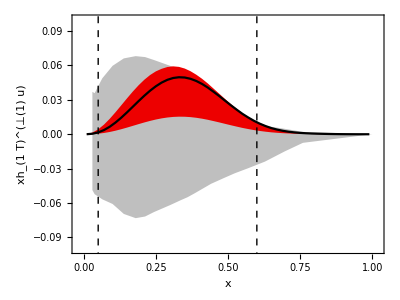

```mathematica
ploth1tMu=Show[uold,unew,VerticleLines]
```

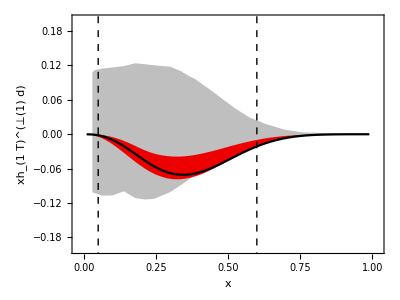

```mathematica
ploth1tMd=Show[dold,dnew,VerticleLines]
```

```mathematica
Export["/Users/user/Documents/SoLID/lpretzel_u.eps",ploth1tMu];
Export["/Users/user/Documents/SoLID/lpretzel_d.eps",ploth1tMd];
```

### Pretzelosity 2

```mathematica
datalist={{0.010000,0.000026,0.000139,-0.000000,-0.000026,-0.000005,-0.000168},{0.030000,0.000440,0.001315,-0.000001,-0.000450,-0.000131,-0.001627},{0.050000,0.001611,0.003890,-0.000004,-0.001715,-0.000591,-0.004708},{0.070000,0.003660,0.007713,-0.000010,-0.004071,-0.001566,-0.009320},{0.090000,0.006563,0.012494,-0.000016,-0.007610,-0.003180,-0.015212},{0.110000,0.010214,0.017926,-0.000025,-0.012291,-0.005487,-0.022047},{0.130000,0.014456,0.023713,-0.000034,-0.017964,-0.008449,-0.029445},{0.150000,0.019109,0.029583,-0.000044,-0.024400,-0.011942,-0.037022},{0.170000,0.023989,0.035303,-0.000054,-0.031316,-0.015868,-0.044658},{0.190000,0.028892,0.040647,-0.000064,-0.038401,-0.019991,-0.052062},{0.210000,0.033625,0.045427,-0.000074,-0.045348,-0.023637,-0.058744},{0.230000,0.038005,0.049489,-0.000082,-0.051862,-0.027063,-0.064460},{0.250000,0.041863,0.052886,-0.000089,-0.057686,-0.030133,-0.069317},{0.270000,0.045066,0.055447,-0.000095,-0.062596,-0.032730,-0.073077},{0.290000,0.047491,0.057013,-0.000099,-0.066439,-0.034770,-0.075513},{0.310000,0.049057,0.057559,-0.000101,-0.069114,-0.036199,-0.076682},{0.330000,0.049721,0.057098,-0.000102,-0.070577,-0.036995,-0.076674},{0.350000,0.049473,0.055676,-0.000100,-0.070836,-0.037157,-0.076080},{0.370000,0.048369,0.053404,-0.000097,-0.069940,-0.036713,-0.074314},{0.390000,0.046461,0.050378,-0.000093,-0.067999,-0.035718,-0.071518},{0.410000,0.043878,0.046766,-0.000087,-0.065133,-0.034233,-0.067947},{0.430000,0.040716,0.042692,-0.000080,-0.061498,-0.032120,-0.063769},{0.450000,0.037034,0.038229,-0.000072,-0.057272,-0.029493,-0.059045},{0.470000,0.033236,0.033800,-0.000064,-0.052570,-0.026708,-0.053899},{0.490000,0.029211,0.029450,-0.000056,-0.047594,-0.023869,-0.048541},{0.510000,0.025245,0.025476,-0.000048,-0.042482,-0.021041,-0.043189},{0.530000,0.021448,0.021740,-0.000041,-0.037375,-0.018292,-0.038050},{0.550000,0.017794,0.018168,-0.000034,-0.032410,-0.015680,-0.033053},{0.570000,0.014619,0.015031,-0.000027,-0.027678,-0.013243,-0.028370},{0.590000,0.011710,0.012122,-0.000022,-0.023279,-0.011020,-0.023995},{0.610000,0.009226,0.009613,-0.000017,-0.019268,-0.009027,-0.020012},{0.630000,0.007153,0.007500,-0.000013,-0.015685,-0.007275,-0.016496},{0.650000,0.005387,0.005683,-0.000010,-0.012549,-0.005764,-0.013361},{0.670000,0.004078,0.004327,-0.000007,-0.009855,-0.004484,-0.010617},{0.690000,0.003004,0.003207,-0.000005,-0.007591,-0.003422,-0.008272},{0.710000,0.002209,0.002371,-0.000004,-0.005726,-0.002559,-0.006309},{0.730000,0.001627,0.001756,-0.000003,-0.004222,-0.001871,-0.004703},{0.750000,0.001174,0.001273,-0.000002,-0.003039,-0.001335,-0.003421},{0.770000,0.000885,0.000965,-0.000002,-0.002129,-0.000928,-0.002422},{0.790000,0.000650,0.000712,-0.000001,-0.001449,-0.000626,-0.001665},{0.810000,0.000479,0.000528,-0.000001,-0.000954,-0.000409,-0.001107},{0.830000,0.000348,0.000385,-0.000001,-0.000606,-0.000258,-0.000710},{0.850000,0.000237,0.000264,-0.000000,-0.000369,-0.000156,-0.000436},{0.870000,0.000157,0.000176,-0.000000,-0.000214,-0.000090,-0.000255},{0.890000,0.000091,0.000103,-0.000000,-0.000117,-0.000049,-0.000141},{0.910000,0.000047,0.000053,-0.000000,-0.000059,-0.000024,-0.000072},{0.930000,0.000019,0.000022,-0.000000,-0.000027,-0.000011,-0.000033},{0.950000,0.000005,0.000006,-0.000000,-0.000010,-0.000004,-0.000012},{0.970000,0.000001,0.000001,-0.000000,-0.000002,-0.000001,-0.000003},{0.990000,0.000000,0.000000,-0.000000,-0.000000,-0.000000,-0.000000}};
ulistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{2}],2];
ulistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{3}],2];
ulistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{4}],2];
dlistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{5}],2];
dlistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{6}],2];
dlistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{7}],2];
```

```mathematica
uoldlist={{0.02991314450408691,0.036552901023890756,0.,-0.049146757679180864,0.000436936},{0.037658417762866055,0.036552901023890756,0.001535836177474402,-0.05150170648464163,0.000788157},{0.0641056859642023,0.04935153583617744,0.0035836177474402714,-0.05610921501706483,0.00296382},{0.1,0.060102389078498256,0.008703071672354946,-0.06040955631399315,0.00830371},{0.1389180315187427,0.06552901023890782,0.01587030716723549,-0.07013651877133104,0.0164968},{0.17995852040347324,0.06624573378839586,0.024573378839590432,-0.07505119453924913,0.0264482},{0.21261123338996563,0.06399317406143341,0.030921501706484618,-0.07505119453924913,0.0342358},{0.2433362979605388,0.060102389078498256,0.036040955631399293,-0.07249146757679178,0.0406688},{0.30008299060449317,0.05447098976109212,0.04325938566552899,-0.06686006825938565,0.0484135},{0.3369660964405174,0.051911262798634776,0.04576791808873717,-0.061433447098976086,0.0497763},{0.36020664817419024,0.04986348122866891,0.04607508532423206,-0.05784982935153581,0.0490598},{0.3856620421163471,0.044744027303754236,0.044744027303754236,-0.0535494880546075,0.0469776},{0.44139517981330917,0.03962457337883956,0.03962457337883956,-0.042286689419795215,0.0387064},{0.487064197188132,0.03430034129692831,0.03430034129692831,-0.03358361774744027,0.0298362},{0.5231433265727812,0.028873720136518746,0.028873720136518746,-0.02795221843003413,0.0227587},{0.5708890645705096,0.022525597269624564,0.022525597269624564,-0.021501706484641628,0.014496},{0.6279586317101167,0.015051194539249128,0.015051194539249128,-0.01617747440273038,0.00735599},{0.6962394391782494,0.00972696245733788,0.007679180887372011,-0.010034129692832771,0.00271616},{0.759783145382949,0.004607508532423206,0.0035836177474402714,-0.004914675767918098,0.00102506},{1.,0.,0.,0.,0.}};
uoldupper=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{2}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
uoldcenter=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{5}],2];
uoldlower=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{4}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
```

```mathematica
doldlist={{0.02991314450408691,0.1079180887372013,-0.0010238907849829347,-0.10197952218430033,-0.000446226},{0.037658417762866055,0.10996587030716716,-0.0026621160409556538,-0.10443686006825935,-0.000817},{0.0641056859642023,0.1109897610921501,-0.006757679180887393,-0.11058020477815696,-0.003254},{0.1,0.10996587030716716,-0.016382252559726956,-0.1132423208191126,-0.009814},{0.1389180315187427,0.10894197952218423,-0.030716723549488043,-0.10955631399317402,-0.0207597},{0.17995852040347324,0.11201365187713304,-0.04668941979522185,-0.12348122866894196,-0.034854},{0.21261123338996563,0.10894197952218423,-0.059385665529010215,-0.12696245733788392,-0.0462486},{0.2433362979605388,0.10750853242320815,-0.06860068259385663,-0.12552901023890783,-0.05586},{0.30008299060449317,0.10587030716723543,-0.0798634812286689,-0.11262798634812282,-0.06799},{0.3369660964405174,0.09931740614334467,-0.08150170648464163,-0.09931740614334467,-0.07085},{0.36020664817419024,0.09255972696245728,-0.08088737201365184,-0.09071672354948804,-0.07057},{0.3856620421163471,0.08703071672354945,-0.07781569965870304,-0.08047781569965869,-0.06856},{0.44139517981330917,0.06962457337883957,-0.0661433447098976,-0.0661433447098976,-0.05921},{0.487064197188132,0.053651877133105756,-0.05385665529010239,-0.05385665529010239,-0.04839},{0.5231433265727812,0.04197952218430032,-0.043003412969283256,-0.043003412969283256,-0.03916},{0.5708890645705096,0.02805460750853239,-0.029692832764505107,-0.029692832764505107,-0.02751},{0.6279586317101167,0.01740614334470989,-0.01699658703071674,-0.01699658703071674,-0.01605},{0.6962394391782494,0.008191126279863478,-0.006757679180887393,-0.006757679180887393,-0.006979},{0.759783145382949,0.003071672354948804,-0.0026621160409556538,-0.0026621160409556538,-0.00256697},{1.,0.,0.,0.,0.}};
doldupper=Join[Take[doldlist,All,{1}],Take[doldlist,All,{2}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}],2];
doldcenter=Join[Take[doldlist,All,{1}],Take[doldlist,All,{5}],2];
doldlower=Join[Take[doldlist,All,{1}],Take[doldlist,All,{4}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}],2];
```

```mathematica
uold=ListPlot[{uoldupper,uoldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.1,0.1}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_(1  T)^(⊥(1) u)",18]},LabelStyle->14];
```

```mathematica
unew=ListPlot[{ulistcenter,ulistupper,ulistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.1,0.1}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

```mathematica
dold=ListPlot[{doldupper,doldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.2,0.2}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_(1  T)^(⊥(1) d)",18]},LabelStyle->14];
```

```mathematica
dnew=ListPlot[{dlistcenter,dlistupper,dlistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.2,0.2}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

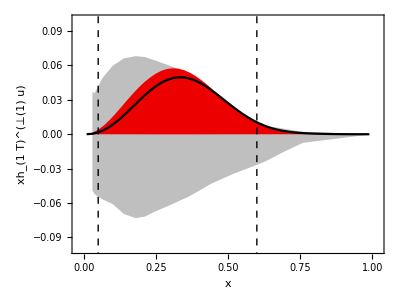

```mathematica
ploth1tMu=Show[uold,unew,VerticleLines]
```

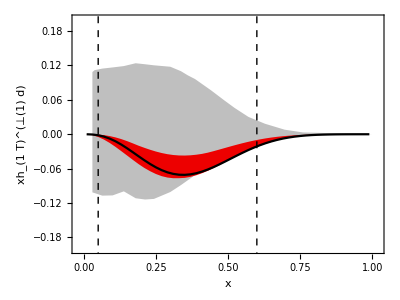

```mathematica
ploth1tMd=Show[dold,dnew,VerticleLines]
```

```mathematica
Export["/Users/user/Documents/SoLID/lpretzel2_u.eps",ploth1tMu];
Export["/Users/user/Documents/SoLID/lpretzel2_d.eps",ploth1tMd];
```

### Transversity

```mathematica
datalist={{0.010000,0.007777,0.009134,0.006274,-0.011545,-0.009268,-0.013528},{0.030000,0.031996,0.035274,0.027024,-0.037950,-0.031632,-0.041267},{0.050000,0.061442,0.066432,0.052252,-0.064269,-0.053938,-0.067722},{0.070000,0.092573,0.098877,0.079039,-0.087345,-0.073595,-0.090367},{0.090000,0.123018,0.130266,0.105297,-0.106005,-0.089543,-0.108730},{0.110000,0.151273,0.159147,0.129695,-0.119715,-0.101290,-0.121996},{0.130000,0.176247,0.184485,0.151266,-0.128499,-0.108836,-0.130417},{0.150000,0.197183,0.205570,0.169338,-0.132712,-0.112474,-0.134304},{0.170000,0.213672,0.222040,0.183549,-0.132847,-0.112620,-0.134052},{0.190000,0.225378,0.233594,0.193607,-0.129607,-0.109873,-0.130400},{0.210000,0.232299,0.240570,0.199507,-0.123653,-0.104802,-0.124041},{0.230000,0.234614,0.242884,0.201410,-0.115637,-0.097968,-0.115658},{0.250000,0.232652,0.240843,0.199606,-0.106187,-0.089907,-0.106452},{0.270000,0.226884,0.234928,0.194510,-0.095833,-0.081079,-0.096478},{0.290000,0.217807,0.225638,0.186559,-0.085103,-0.071936,-0.086068},{0.310000,0.206011,0.213571,0.176271,-0.074412,-0.062833,-0.075624},{0.330000,0.192106,0.199342,0.164180,-0.064101,-0.054063,-0.065485},{0.350000,0.176691,0.183687,0.150809,-0.054416,-0.045835,-0.055921},{0.370000,0.160348,0.167176,0.136665,-0.045527,-0.038293,-0.047112},{0.390000,0.143595,0.150573,0.122197,-0.037561,-0.031544,-0.039162},{0.410000,0.126906,0.133977,0.107814,-0.030555,-0.025617,-0.032118},{0.430000,0.110684,0.117705,0.093863,-0.024518,-0.020518,-0.025998},{0.450000,0.095258,0.102092,0.080626,-0.019419,-0.016220,-0.020786},{0.470000,0.080876,0.087402,0.068200,-0.015151,-0.012629,-0.016380},{0.490000,0.067724,0.073842,0.056734,-0.011661,-0.009699,-0.012742},{0.510000,0.055905,0.061534,0.046509,-0.008846,-0.007312,-0.009777},{0.530000,0.045470,0.050554,0.037551,-0.006613,-0.005426,-0.007398},{0.550000,0.036419,0.040926,0.029843,-0.004876,-0.003970,-0.005525},{0.570000,0.028687,0.032607,0.023316,-0.003545,-0.002863,-0.004072},{0.590000,0.022212,0.025600,0.017898,-0.002545,-0.002037,-0.002967},{0.610000,0.016879,0.019759,0.013476,-0.001806,-0.001433,-0.002138},{0.630000,0.012571,0.014962,0.009939,-0.001269,-0.000997,-0.001528},{0.650000,0.009163,0.011100,0.007170,-0.000884,-0.000688,-0.001084},{0.670000,0.006516,0.008046,0.005043,-0.000613,-0.000471,-0.000765},{0.690000,0.004515,0.005690,0.003453,-0.000422,-0.000320,-0.000537},{0.710000,0.003037,0.003912,0.002293,-0.000289,-0.000216,-0.000376},{0.730000,0.001975,0.002606,0.001471,-0.000196,-0.000145,-0.000261},{0.750000,0.001238,0.001675,0.000908,-0.000131,-0.000096,-0.000180},{0.770000,0.000741,0.001032,0.000535,-0.000087,-0.000062,-0.000122},{0.790000,0.000422,0.000606,0.000298,-0.000055,-0.000039,-0.000081},{0.810000,0.000226,0.000336,0.000155,-0.000034,-0.000024,-0.000052},{0.830000,0.000112,0.000174,0.000074,-0.000020,-0.000013,-0.000032},{0.850000,0.000051,0.000082,0.000032,-0.000011,-0.000007,-0.000018},{0.870000,0.000021,0.000035,0.000012,-0.000006,-0.000003,-0.000010},{0.890000,0.000007,0.000013,0.000004,-0.000003,-0.000001,-0.000005},{0.910000,0.000002,0.000004,0.000001,-0.000001,-0.000001,-0.000002},{0.930000,0.000000,0.000001,0.000000,-0.000000,-0.000000,-0.000001},{0.950000,0.000000,0.000000,0.000000,-0.000000,-0.000000,-0.000000},{0.970000,0.000000,0.000000,0.000000,-0.000000,-0.000000,-0.000000},{0.990000,0.000000,0.000000,0.000000,-0.000000,-0.000000,-0.000000}};
ulistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{2}],2];
ulistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{3}],2];
ulistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{4}],2];
dlistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{5}],2];
dlistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{6}],2];
dlistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{7}],2];
```

```mathematica
uoldlist={{0,0,0,0,0},{0.001054888969316595,0.005373134328358243,0.,0.,0.000613259},{0.010024318393651338,0.021492537313432803,0.006567164179104443,0.0014925373134328358,0.00780783},{0.04012134905082846,0.0588059701492537,0.03761194029850753,0.02417910447761201,0.0465955},{0.1,0.15731343283582086,0.11373134328358216,0.08268656716417908,0.137425},{0.1453607842411577,0.22447761194029847,0.16358208955223885,0.11880597014925377,0.192734},{0.20127853758499395,0.2656716417910448,0.20089552238805974,0.13731343283582090,0.229787},{0.21387931099785842,0.2743283582089552,0.2044776119402985,0.1373134328358209,0.233046},{0.2362749726243278,0.28298507462686573,0.20835820895522392,0.1310447761194029,0.23438},{0.27534260550056244,0.2844776119402985,0.2032835820895523,0.11492537313432837,0.224659},{0.32086999973704494,0.2817910447761193,0.18208955223880596,0.08119402985074624,0.198579},{0.38498431685855317,0.2594029850746268,0.1411940298507463,0.039104477611940365,0.147711},{0.4252966708288167,0.23820895522388064,0.11134328358208959,0.021492537313432803,0.114351},{0.4896360860681199,0.19134328358208963,0.06895522388059708,0.007462686567164179,0.0678911},{0.5165117061726114,0.16985074626865665,0.054029850746268725,0.004477611940298508,0.0523043},{0.5569043250260577,0.1334328358208955,0.034328358208955224,0.0017910447761194709,0.0335666},{0.6152187115995491,0.09223880597014919,0.01671641791044783,0.0008955223880597354,0.0156423},{0.679639295465157,0.054029850746268725,0.006567164179104443,0.0008955223880597354,0.00547167},{0.7327889350405573,0.029850746268656716,0.0026865671641790366,0.00029850746268663504,0.00185202},{0.7900950208453675,0.014925373134328358,0.0008955223880597354,0.00029850746268663504,0.000420206},{1.,0.,0.,0.,0.}};
uoldupper=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{2}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
uoldcenter=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{5}],2];
uoldlower=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{4}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
```

```mathematica
doldlist={{0,0,0,0,0},{0.0019502235127820703,0.001791044776119386,-0.001791044776119386,-0.014925373134328358,-0.00218362},{0.005004573692213212,0.0029850746268656717,-0.004776119402985057,-0.024179104477611922,-0.00558844},{0.01,0.0038805970149254072,-0.0101492537313433,-0.03373134328358204,-0.0115571},{0.014084264654587899,0.004776119402985057,-0.014029850746268623,-0.040000000000000015,-0.0167158},{0.05330810554921807,0.012238805970149237,-0.05402985074626864,-0.0746268656716418,-0.0683326},{0.09927398216684538,0.016716417910447746,-0.08955223880597014,-0.10656716417910445,-0.113037},{0.12085885653790494,0.018805970149253764,-0.1,-0.11283582089552234,-0.125064,-0.125064},{0.14187266741165955,0.019701492537313417,-0.10537313432835815,-0.11671641791044775,-0.131457},{0.1689849786812458,0.019701492537313417,-0.10746268656716418,-0.11283582089552234,-0.132873},{0.19836651086047374,0.018805970149253764,-0.10358208955223877,-0.1044776119402985,-0.127367},{0.23285662984981959,0.015820895522388093,-0.0943283582089552,-0.0943283582089552,-0.114287},{0.27268045402016744,0.013134328358208972,-0.07940298507462686,-0.08119402985074624,-0.0943477},{0.3012332820234747,0.011343283582089586,-0.06805970149253726,-0.07194029850746267,-0.0790217},{0.33277592456965444,0.009253731343283566,-0.054925373134328374,-0.06149253731343282,-0.0626541},{0.3757461287066558,0.007462686567164179,-0.03910447761194028,-0.04955223880597013,-0.0431031},{0.42118468765136446,0.005671641791044793,-0.027164179104477597,-0.03910447761194028,-0.0270277},{0.467553404457158,0.0038805970149254072,-0.01582089552238801,-0.029850746268656716,-0.0156093},{0.5292107919641389,0.0029850746268656717,-0.00835820895522383,-0.01761194029850748,-0.00668198},{0.591768574818882,0.001791044776119386,-0.0026865671641791216,-0.0101492537313433,-0.00246611},{1.,0.,0.,0.,0.}};
doldupper=Join[Take[doldlist,All,{1}],Take[doldlist,All,{2}](*+Take[doldlist,All,{5}]-Take[doldlist,All,{3}]*),2];
doldcenter=Join[Take[doldlist,All,{1}],Take[doldlist,All,{5}],2];
doldlower=Join[Take[doldlist,All,{1}],Take[doldlist,All,{4}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}],2];
```

```mathematica
uold=ListPlot[{uoldupper,uoldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.01,0.35}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_1^u(x)",18]},LabelStyle->14];
```

```mathematica
unew=ListPlot[{ulistcenter,ulistupper,ulistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.01,0.35}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

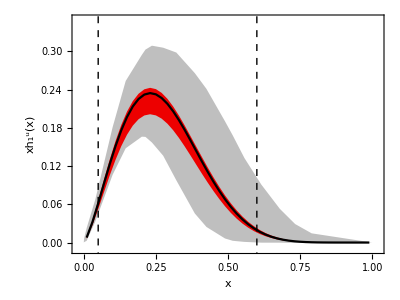

```mathematica
ploth1u=Show[uold,unew,VerticleLines]
```

```mathematica
dold=ListPlot[{doldupper,doldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.25,0.15}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_1^d(x)",18]},LabelStyle->14];
```

```mathematica
dnew=ListPlot[{dlistcenter,dlistupper,dlistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.25,0.15}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

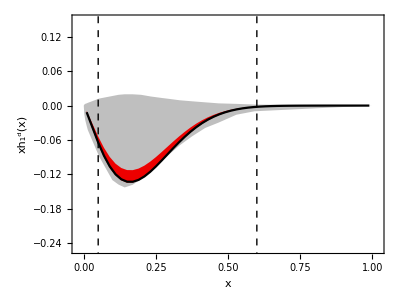

```mathematica
ploth1d=Show[dold,dnew,VerticleLines]
```

```mathematica
Export["/Users/user/Documents/SoLID/ltrans_u.eps",ploth1u];
Export["/Users/user/Documents/SoLID/ltrans_d.eps",ploth1d];
```

### Transversity 2

```mathematica
datalist={{0.010000,0.007777,0.009640,0.006325,-0.011545,-0.009309,-0.013358},{0.030000,0.031996,0.037769,0.027775,-0.037950,-0.032907,-0.040825},{0.050000,0.061442,0.071040,0.053836,-0.064269,-0.057092,-0.067068},{0.070000,0.092573,0.106103,0.081599,-0.087345,-0.078400,-0.089547},{0.090000,0.123018,0.140795,0.108908,-0.106005,-0.095780,-0.107520},{0.110000,0.151273,0.172935,0.134376,-0.119715,-0.108634,-0.121190},{0.130000,0.176247,0.201294,0.156990,-0.128499,-0.116927,-0.129886},{0.150000,0.197183,0.225023,0.176039,-0.132712,-0.120363,-0.133902},{0.170000,0.213672,0.243668,0.191128,-0.132847,-0.120168,-0.133766},{0.190000,0.225378,0.256858,0.201934,-0.129607,-0.117027,-0.130210},{0.210000,0.232299,0.264598,0.208434,-0.123653,-0.111529,-0.123980},{0.230000,0.234614,0.267102,0.210776,-0.115637,-0.104249,-0.115710},{0.250000,0.232652,0.264747,0.209242,-0.106187,-0.095605,-0.106259},{0.270000,0.226884,0.258076,0.204251,-0.095833,-0.085923,-0.095987},{0.290000,0.217807,0.247655,0.196245,-0.085103,-0.075952,-0.085521},{0.310000,0.206011,0.234159,0.185755,-0.074412,-0.066076,-0.075109},{0.330000,0.192106,0.218282,0.173329,-0.064101,-0.056610,-0.065032},{0.350000,0.176691,0.200705,0.158879,-0.054416,-0.047777,-0.055504},{0.370000,0.160348,0.182141,0.143557,-0.045527,-0.039723,-0.046700},{0.390000,0.143595,0.163948,0.127955,-0.037561,-0.032554,-0.038756},{0.410000,0.126906,0.145684,0.112514,-0.030555,-0.026296,-0.031723},{0.430000,0.110684,0.127798,0.097443,-0.024518,-0.020942,-0.025620},{0.450000,0.095258,0.110662,0.082892,-0.019419,-0.016457,-0.020438},{0.470000,0.080876,0.094564,0.069517,-0.015151,-0.012732,-0.016076},{0.490000,0.067724,0.079731,0.057462,-0.011661,-0.009713,-0.012481},{0.510000,0.055905,0.066427,0.046788,-0.008846,-0.007300,-0.009557},{0.530000,0.045470,0.054779,0.037508,-0.006613,-0.005402,-0.007216},{0.550000,0.036419,0.044521,0.029585,-0.004876,-0.003922,-0.005377},{0.570000,0.028687,0.035618,0.022931,-0.003545,-0.002806,-0.003954},{0.590000,0.022212,0.028038,0.017454,-0.002545,-0.001980,-0.002873},{0.610000,0.016879,0.021684,0.013025,-0.001806,-0.001380,-0.002065},{0.630000,0.012571,0.016455,0.009515,-0.001269,-0.000951,-0.001471},{0.650000,0.009163,0.012236,0.006794,-0.000884,-0.000649,-0.001040},{0.670000,0.006516,0.008890,0.004727,-0.000613,-0.000440,-0.000732},{0.690000,0.004515,0.006303,0.003200,-0.000422,-0.000296,-0.000513},{0.710000,0.003037,0.004345,0.002098,-0.000289,-0.000197,-0.000358},{0.730000,0.001975,0.002902,0.001328,-0.000196,-0.000130,-0.000249},{0.750000,0.001238,0.001872,0.000808,-0.000131,-0.000085,-0.000171},{0.770000,0.000741,0.001157,0.000469,-0.000087,-0.000054,-0.000116},{0.790000,0.000422,0.000682,0.000258,-0.000055,-0.000034,-0.000077},{0.810000,0.000226,0.000380,0.000133,-0.000034,-0.000020,-0.000049},{0.830000,0.000112,0.000197,0.000063,-0.000020,-0.000011,-0.000030},{0.850000,0.000051,0.000094,0.000027,-0.000011,-0.000006,-0.000017},{0.870000,0.000021,0.000040,0.000010,-0.000006,-0.000003,-0.000009},{0.890000,0.000007,0.000015,0.000003,-0.000003,-0.000001,-0.000004},{0.910000,0.000002,0.000004,0.000001,-0.000001,-0.000000,-0.000002},{0.930000,0.000000,0.000001,0.000000,-0.000000,-0.000000,-0.000001},{0.950000,0.000000,0.000000,0.000000,-0.000000,-0.000000,-0.000000},{0.970000,0.000000,0.000000,0.000000,-0.000000,-0.000000,-0.000000},{0.990000,0.000000,0.000000,0.000000,-0.000000,-0.000000,-0.000000}};
ulistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{2}],2];
ulistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{3}],2];
ulistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{4}],2];
dlistcenter=Join[Take[datalist,All,{1}],Take[datalist,All,{5}],2];
dlistupper=Join[Take[datalist,All,{1}],Take[datalist,All,{6}],2];
dlistlower=Join[Take[datalist,All,{1}],Take[datalist,All,{7}],2];
```

```mathematica
uoldlist={{0,0,0,0,0},{0.001054888969316595,0.005373134328358243,0.,0.,0.000613259},{0.010024318393651338,0.021492537313432803,0.006567164179104443,0.0014925373134328358,0.00780783},{0.04012134905082846,0.0588059701492537,0.03761194029850753,0.02417910447761201,0.0465955},{0.1,0.15731343283582086,0.11373134328358216,0.08268656716417908,0.137425},{0.1453607842411577,0.22447761194029847,0.16358208955223885,0.11880597014925377,0.192734},{0.20127853758499395,0.2656716417910448,0.20089552238805974,0.13731343283582090,0.229787},{0.21387931099785842,0.2743283582089552,0.2044776119402985,0.1373134328358209,0.233046},{0.2362749726243278,0.28298507462686573,0.20835820895522392,0.1310447761194029,0.23438},{0.27534260550056244,0.2844776119402985,0.2032835820895523,0.11492537313432837,0.224659},{0.32086999973704494,0.2817910447761193,0.18208955223880596,0.08119402985074624,0.198579},{0.38498431685855317,0.2594029850746268,0.1411940298507463,0.039104477611940365,0.147711},{0.4252966708288167,0.23820895522388064,0.11134328358208959,0.021492537313432803,0.114351},{0.4896360860681199,0.19134328358208963,0.06895522388059708,0.007462686567164179,0.0678911},{0.5165117061726114,0.16985074626865665,0.054029850746268725,0.004477611940298508,0.0523043},{0.5569043250260577,0.1334328358208955,0.034328358208955224,0.0017910447761194709,0.0335666},{0.6152187115995491,0.09223880597014919,0.01671641791044783,0.0008955223880597354,0.0156423},{0.679639295465157,0.054029850746268725,0.006567164179104443,0.0008955223880597354,0.00547167},{0.7327889350405573,0.029850746268656716,0.0026865671641790366,0.00029850746268663504,0.00185202},{0.7900950208453675,0.014925373134328358,0.0008955223880597354,0.00029850746268663504,0.000420206},{1.,0.,0.,0.,0.}};
uoldupper=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{2}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
uoldcenter=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{5}],2];
uoldlower=Join[Take[uoldlist,All,{1}],Take[uoldlist,All,{4}]+Take[uoldlist,All,{5}]-Take[uoldlist,All,{3}],2];
```

```mathematica
doldlist={{0,0,0,0,0},{0.0019502235127820703,0.001791044776119386,-0.001791044776119386,-0.014925373134328358,-0.00218362},{0.005004573692213212,0.0029850746268656717,-0.004776119402985057,-0.024179104477611922,-0.00558844},{0.01,0.0038805970149254072,-0.0101492537313433,-0.03373134328358204,-0.0115571},{0.014084264654587899,0.004776119402985057,-0.014029850746268623,-0.040000000000000015,-0.0167158},{0.05330810554921807,0.012238805970149237,-0.05402985074626864,-0.0746268656716418,-0.0683326},{0.09927398216684538,0.016716417910447746,-0.08955223880597014,-0.10656716417910445,-0.113037},{0.12085885653790494,0.018805970149253764,-0.1,-0.11283582089552234,-0.125064,-0.125064},{0.14187266741165955,0.019701492537313417,-0.10537313432835815,-0.11671641791044775,-0.131457},{0.1689849786812458,0.019701492537313417,-0.10746268656716418,-0.11283582089552234,-0.132873},{0.19836651086047374,0.018805970149253764,-0.10358208955223877,-0.1044776119402985,-0.127367},{0.23285662984981959,0.015820895522388093,-0.0943283582089552,-0.0943283582089552,-0.114287},{0.27268045402016744,0.013134328358208972,-0.07940298507462686,-0.08119402985074624,-0.0943477},{0.3012332820234747,0.011343283582089586,-0.06805970149253726,-0.07194029850746267,-0.0790217},{0.33277592456965444,0.009253731343283566,-0.054925373134328374,-0.06149253731343282,-0.0626541},{0.3757461287066558,0.007462686567164179,-0.03910447761194028,-0.04955223880597013,-0.0431031},{0.42118468765136446,0.005671641791044793,-0.027164179104477597,-0.03910447761194028,-0.0270277},{0.467553404457158,0.0038805970149254072,-0.01582089552238801,-0.029850746268656716,-0.0156093},{0.5292107919641389,0.0029850746268656717,-0.00835820895522383,-0.01761194029850748,-0.00668198},{0.591768574818882,0.001791044776119386,-0.0026865671641791216,-0.0101492537313433,-0.00246611},{1.,0.,0.,0.,0.}};
doldupper=Join[Take[doldlist,All,{1}],Take[doldlist,All,{2}](*+Take[doldlist,All,{5}]-Take[doldlist,All,{3}]*),2];
doldcenter=Join[Take[doldlist,All,{1}],Take[doldlist,All,{5}],2];
doldlower=Join[Take[doldlist,All,{1}],Take[doldlist,All,{4}]+Take[doldlist,All,{5}]-Take[doldlist,All,{3}],2];
```

```mathematica
uold=ListPlot[{uoldupper,uoldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.01,0.35}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_1^u(x)",18]},LabelStyle->14];
```

```mathematica
unew=ListPlot[{ulistcenter,ulistupper,ulistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.01,0.35}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

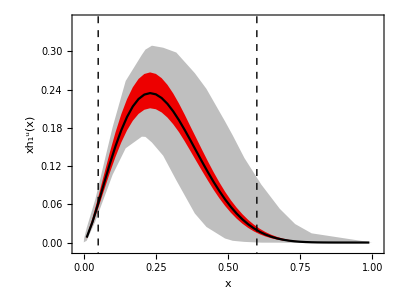

```mathematica
ploth1u=Show[uold,unew,VerticleLines]
```

```mathematica
dold=ListPlot[{doldupper,doldlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.25,0.15}},PlotStyle->{None,None},FrameLabel->{Style["x",18],Style["xh_1^d(x)",18]},LabelStyle->14];
```

```mathematica
dnew=ListPlot[{dlistcenter,dlistupper,dlistlower},Frame->True,FrameStyle->Thickness[0.0025],Joined->True,AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.25,0.15}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
```

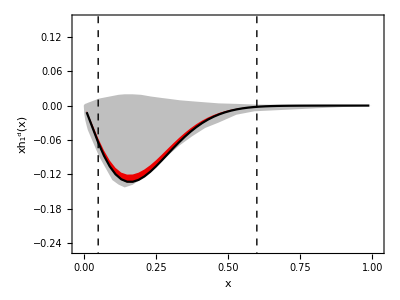

```mathematica
ploth1d=Show[dold,dnew,VerticleLines]
```

```mathematica
Export["/Users/user/Documents/SoLID/ltrans2_u.eps",ploth1u];
Export["/Users/user/Documents/SoLID/ltrans2_d.eps",ploth1d];
```

```mathematica
xh1kt[a0_,kt_]:=a0 Exp[-kt^2/0.25]/(0.25 π) (2 kt)/0.93827;
```

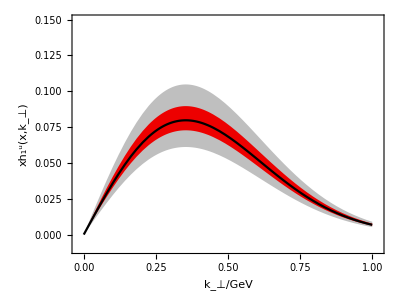

```mathematica
uold=Plot[{xh1kt[0.180,kt],xh1kt[0.105,kt]},{kt,0,1},Frame->True,FrameStyle->Thickness[0.0025],AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.01,0.15}},PlotStyle->{None,None},FrameLabel->{Style["k_⊥/GeV",18],Style["xh_1^u(x,k_⊥)",18]},LabelStyle->14];
unew=Plot[{xh1kt[0.137,kt],xh1kt[0.154,kt],xh1kt[0.125,kt]},{kt,0,1},Frame->True,FrameStyle->Thickness[0.0025],AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.01,0.15}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
ploth1ukt=Show[uold,unew]
```

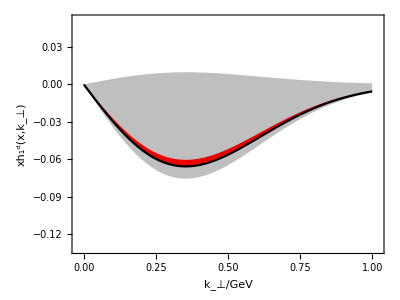

```mathematica
dold=Plot[{xh1kt[0.0167,kt],xh1kt[-0.1299,kt]},{kt,0,1},Frame->True,FrameStyle->Thickness[0.0025],AspectRatio->0.75,Filling->{1->{2}},FillingStyle->Lighter[Gray,0.5],PlotRange->{{-0.02,1.02},{-0.132,0.052}},PlotStyle->{None,None},FrameLabel->{Style["k_⊥/GeV",18],Style["xh_1^d(x,k_⊥)",18]},LabelStyle->14];
dnew=Plot[{xh1kt[-0.113,kt],xh1kt[-0.104,kt],xh1kt[-0.114,kt]},{kt,0,1},Frame->True,FrameStyle->Thickness[0.0025],AspectRatio->0.75,Filling->{2->{3}},FillingStyle->Darker[Red,0.07],PlotRange->{{-0.02,1.02},{-0.25,0.15}},PlotStyle->{{Black,Thickness[0.004]},None,None}];
ploth1dkt=Show[dold,dnew]
```

```mathematica
Export["/Users/user/Documents/SoLID/ltrans2_u_kt.eps",ploth1ukt];
Export["/Users/user/Documents/SoLID/ltrans2_d_kt.eps",ploth1dkt];
```

## Binning

```mathematica
fn[As_,ac_]:=2.0/(0.6 ac As)^2;
```

```mathematica
fn[0.007,0.05]
```

4.53515×10^7

```mathematica
Sqrt[2./(1.4*10^8)]/0.004
```

0.0298807

## Parametrization figures

### Transversity PRD87 (2013) 094019

-Graphics-

```mathematica
origin={392.3,315.5};
scale={392.3-297.5,3490-3155.};
```

```mathematica
cood[{x_,y1_,y2_,y3_}]:={10^((x-origin[[1]])/scale[[1]]),(y1-origin[[2]])/scale[[2]],(y2-origin[[2]])/scale[[2]],(y3-origin[[2]])/scale[[2]]};
```

```mathematica
test=Map[cood,{{110.1,317.3,315.5,315.5},
	{202.8,322.7,317.7,316.0},
	{259.9,335.2,328.1,323.6},
	{297.5,368.2,353.6,343.2},
	{312.9,390.7,370.3,355.3},
	{326.3,404.5,382.8,361.5},
	{328.8,407.4,384.0,361.5},
	{332.9,410.3,385.3,359.4},
	{339.2,410.8,383.6,354.0},
	{345.5,409.9,376.5,342.7},
	{353.0,402.4,362.8,328.6},
	{357.1,395.3,352.8,322.7},
	{362.9,379.6,338.6,318.0},
	{365.1,372.4,333.6,317.0},
	{368.2,360.2,327.0,316.1},
	{372.3,346.4,321.1,315.8},
	{376.4,333.6,317.7,315.8},
	{379.5,325.5,316.4,315.6},
	{382.6,320.5,315.8,315.6},
	{392.3,315.5,315.5,315.5}}]//InputForm
```

{{0.001054888969316595, 
  0.005373134328358243, 0., 0.}, 
 {0.010024318393651338, 
  0.021492537313432803, 
  0.006567164179104443, 
  0.0014925373134328358}, 
 {0.04012134905082846, 
  0.0588059701492537, 
  0.03761194029850753, 
  0.02417910447761201}, 
 {0.1, 0.15731343283582086, 
  0.11373134328358216, 
  0.08268656716417908}, 
 {0.1453607842411577, 
  0.22447761194029847, 
  0.16358208955223885, 
  0.11880597014925377}, 
 {0.20127853758499395, 
  0.2656716417910448, 
  0.20089552238805974, 
  0.1373134328358209}, 
 {0.21387931099785842, 
  0.2743283582089552, 
  0.2044776119402985, 
  0.1373134328358209}, 
 {0.2362749726243278, 
  0.28298507462686573, 
  0.20835820895522392, 
  0.1310447761194029}, 
 {0.27534260550056244, 
  0.2844776119402985, 
  0.2032835820895523, 
  0.11492537313432837}, 
 {0.32086999973704494, 
  0.2817910447761193, 
  0.18208955223880596, 
  0.08119402985074624}, 
 {0.38498431685855317, 
  0.2594029850746268, 
  0.1411940298507463, 
  0.039104477611940365}, 
 {0.4252966708288167, 
  0.23820895522388064, 
  0.11134328358208959, 
  0.021492537313432803}, 
 {0.4896360860681199, 
  0.19134328358208963, 
  0.06895522388059708, 
  0.007462686567164179}, 
 {0.5165117061726114, 
  0.16985074626865665, 
  0.054029850746268725, 
  0.004477611940298508}, 
 {0.5569043250260577, 
  0.1334328358208955, 
  0.034328358208955224, 
  0.0017910447761194709}, 
 {0.6152187115995491, 
  0.09223880597014919, 
  0.01671641791044783, 
  0.0008955223880597354}, 
 {0.679639295465157, 
  0.054029850746268725, 
  0.006567164179104443, 
  0.0008955223880597354}, 
 {0.7327889350405573, 
  0.029850746268656716, 
  0.0026865671641790366, 
  0.00029850746268663504}, 
 {0.7900950208453675, 
  0.014925373134328358, 
  0.0008955223880597354, 
  0.00029850746268663504}, 
 {1., 0., 0., 0.}}

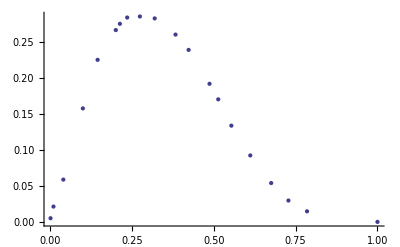

```mathematica
ListPlot[Join[Take[test,All,{1}],Take[test,All,{2}],2]]
```

```mathematica
Join[Take[test,All,{1}],Take[test,All,{2}],2]
```

Join::headsd: Expression TraditionalForm`( GridBox[{{ at position 1 is expected to have head TraditionalForm for all subexpressions through level 2.

Join[(0.00106247 | 0.00508982),(0.0100486 | 0.0212575),2]

### Sivers EPJA 39 (2009) 89

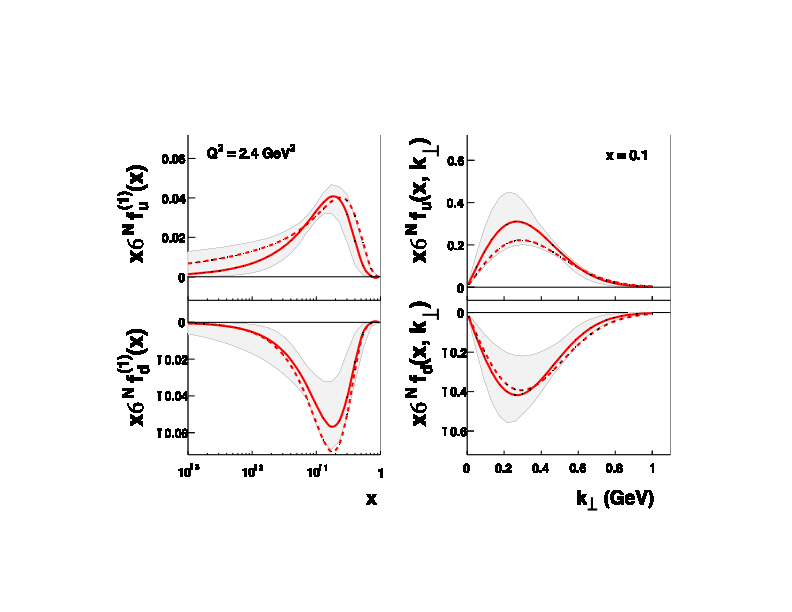

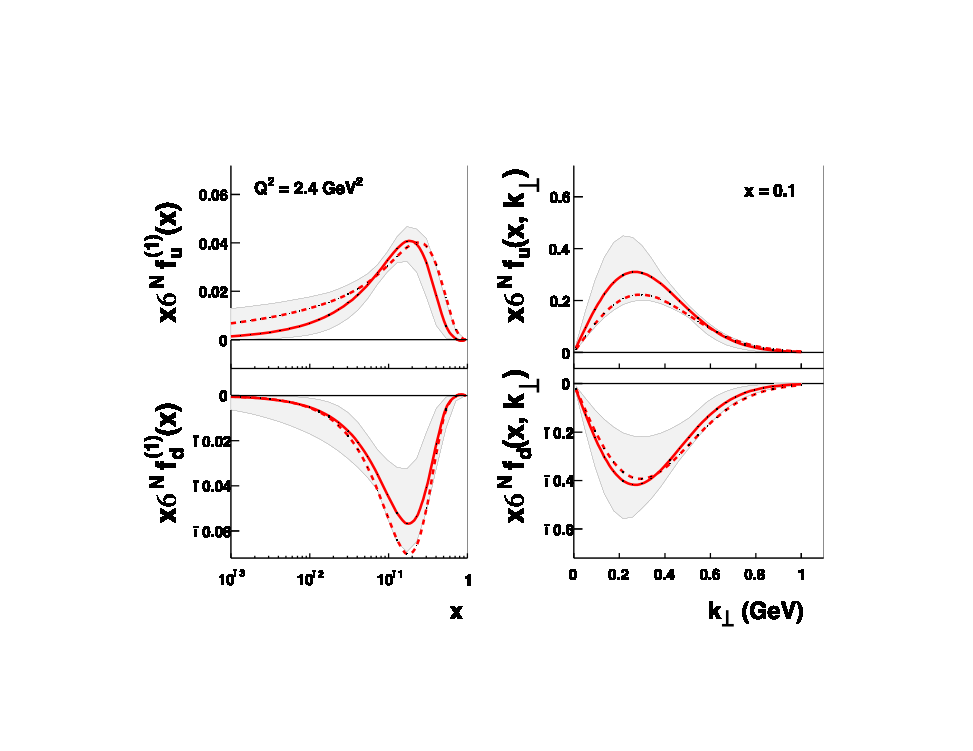

```mathematica
origin={483.2,297.8};
scale={709.6-483.2,(297.8-249.5)/0.2};
```

```mathematica
cood[{x_,y1_,y2_,y3_}]:={10^((x-origin[[1]])/scale[[1]]),(y1-origin[[2]])/scale[[2]],(y2-origin[[2]])/scale[[2]],(y3-origin[[2]])/scale[[2]]};
licood[{x_,y1_,y2_,y3_}]:={(x-origin[[1]])/scale[[1]],(y1-origin[[2]])/scale[[2]],(y2-origin[[2]])/scale[[2]],(y3-origin[[2]])/scale[[2]]};
```

```mathematica
Map[licood,{{483.2,297.8,297.8,297.8},
	{494.9,282.9,266.6,248.7},
	{504.1,271.5,244.0,215.0},
	{513.3,262.2,224.8,188.1},
	{522.8,254.6,210.4,171.0},
	{531.8,248.7,201.1,163.4},
	{541.6,245.7,197.1,164.8},
	{550.8,244.9,198.2,173.2},
	{560.0,245.7,203.0,183.0},
	{569.5,248.4,211.5,194.9},
	{578.8,252.5,221.8,208.2},
	{588.0,257.3,232.9,221.2},
	{597.5,263.6,244.0,233.2},
	{606.7,271.7,254.9,244.6},
	{615.9,279.9,264.4,255.4},
	{625.4,285.8,272.5,264.7},
	{635.0,289.9,279.3,272.8},
	{644.2,293.2,284.5,279.3},
	{653.7,295.1,288.6,284.2},
	{662.9,296.2,291.5,288.0},
	{672.1,297.0,293.7,290.7},
	{690.9,297.5,296.2,294.5},
	{709.6,297.8,297.0,296.2}}]//InputForm
```

{{0., 0., 0., 0.}, {0.05167844522968192, -0.061697722567287915, 
  -0.12919254658385088, -0.203312629399586}, 
 {0.09231448763250898, -0.10890269151138719, -0.22277432712215323, 
  -0.34285714285714286}, {0.13295053003533552, -0.14741200828157358, 
  -0.3022774327122153, -0.45424430641821945}, 
 {0.174911660777385, -0.1788819875776398, -0.3619047619047619, 
  -0.5250517598343685}, {0.2146643109540634, -0.203312629399586, 
  -0.40041407867494827, -0.5565217391304347}, 
 {0.2579505300353358, -0.2157349896480332, -0.41697722567287787, 
  -0.5507246376811593}, {0.29858657243816233, -0.21904761904761905, 
  -0.41242236024844725, -0.5159420289855072}, 
 {0.3392226148409894, -0.2157349896480332, -0.39254658385093166, 
  -0.47536231884057967}, {0.38118374558303886, -0.20455486542443063, 
  -0.3573498964803313, -0.4260869565217391}, 
 {0.4222614840989397, -0.1875776397515528, -0.31469979296066247, 
  -0.37101449275362325}, {0.46289752650176674, -0.16770186335403725, 
  -0.26873706004140785, -0.317184265010352}, 
 {0.5048586572438162, -0.14161490683229808, -0.22277432712215323, 
  -0.2674948240165632}, {0.5454946996466433, -0.10807453416149077, 
  -0.17763975155279502, -0.22028985507246382}, 
 {0.5861307420494698, -0.07412008281573512, -0.13830227743271234, 
  -0.17556935817805383}, {0.6280918727915192, -0.049689440993788817, 
  -0.10476190476190479, -0.13706004140786757}, 
 {0.6704946996466431, -0.03271221532091111, -0.07660455486542442, 
  -0.10351966873706003}, {0.7111307420494701, -0.01904761904761914, 
  -0.05507246376811598, -0.07660455486542442}, 
 {0.7530918727915196, -0.011180124223602437, -0.03809523809523804, 
  -0.05631469979296075}, {0.7937279151943462, -0.006625258799171936, 
  -0.026086956521739174, -0.040579710144927575}, 
 {0.8343639575971732, -0.003312629399585968, -0.01697722567287794, 
  -0.029399585921325144}, {0.9174028268551235, -0.0012422360248447674, 
  -0.006625258799171936, -0.01366459627329197}, 
 {1., 0., -0.003312629399585968, -0.006625258799171936}}

```mathematica
NumberForm[Take[%,All,{1}],4]//TraditionalForm
```

(0.
0.05168
0.09231
0.133
0.1749
0.2147
0.258
0.2986
0.3392
0.3812
0.4223
0.4629
0.5049
0.5455
0.5861
0.6281
0.6705
0.7111
0.7531
0.7937
0.8344
0.9174
1.)

### Pretzelosity PRD 91 (2015) 034010

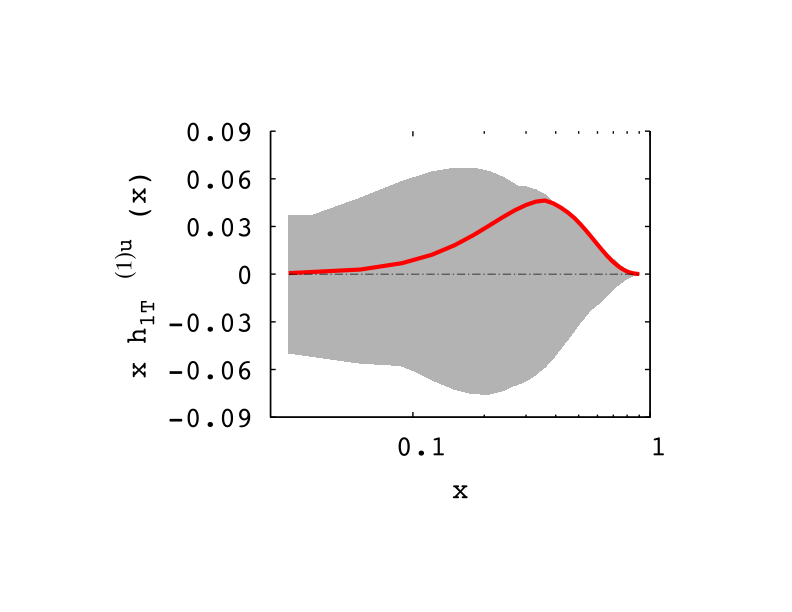

-Graphics-

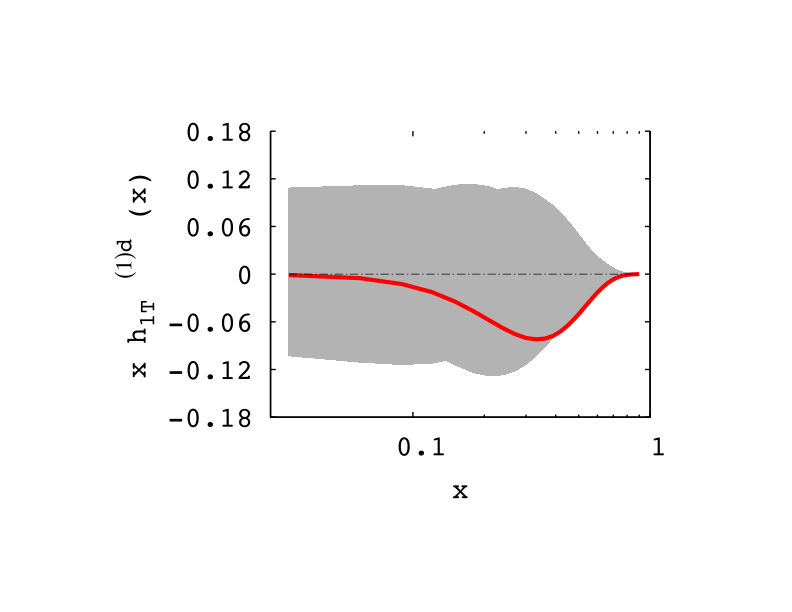

-Graphics-

```mathematica
origin={706.8,344.8};
scale={706.8-416.8,(344.8-286.2)/0.06};
```

```mathematica
cood[{x_,y1_,y2_,y3_}]:={10^((x-origin[[1]])/scale[[1]]),(y1-origin[[2]])/scale[[2]],(y2-origin[[2]])/scale[[2]],(y3-origin[[2]])/scale[[2]]};
```

```mathematica
tt=Map[cood,{{264.8,450.2,343.8,245.2},
	{293.8,452.2,342.2,242.8},
	{360.8,453.2,338.2,236.8},
	{416.8,452.2,328.8,234.2},
	{458.2,451.2,314.8,237.8},
	{490.8,454.2,299.2,224.2},
	{511.8,451.2,286.8,220.8},
	{528.8,449.8,277.8,222.2},
	{555.2,448.2,266.8,234.8},
	{569.8,441.8,265.2,247.8},
	{578.2,435.2,265.8,256.2},
	{586.8,429.8,268.8,266.2},
	{603.8,412.8,280.2,280.2},
	{616.2,397.2,292.2,292.2},
	{625.2,385.8,302.8,302.8},
	{636.2,372.2,315.8,315.8},
	{648.2,361.8,328.2,328.2},
	{661.2,352.8,338.2,338.2},
	{672.2,347.8,342.2,342.2},
	{706.8,344.8,344.8,344.8}}]//InputForm
```

{{0.02991314450408691, 
  0.1079180887372013, 
  -0.0010238907849829347, 
  -0.10197952218430033}, 
 {0.037658417762866055, 
  0.10996587030716716, 
  -0.0026621160409556538, 
  -0.10443686006825935}, 
 {0.0641056859642023, 
  0.1109897610921501, 
  -0.006757679180887393, 
  -0.11058020477815696}, 
 {0.1, 0.10996587030716716, 
  -0.016382252559726956, 
  -0.1132423208191126}, 
 {0.1389180315187427, 
  0.10894197952218423, 
  -0.030716723549488043, 
  -0.10955631399317402}, 
 {0.17995852040347324, 
  0.11201365187713304, 
  -0.04668941979522185, 
  -0.12348122866894196}, 
 {0.21261123338996563, 
  0.10894197952218423, 
  -0.059385665529010215, 
  -0.12696245733788392}, 
 {0.2433362979605388, 
  0.10750853242320815, 
  -0.06860068259385663, 
  -0.12552901023890783}, 
 {0.30008299060449317, 
  0.10587030716723543, 
  -0.0798634812286689, 
  -0.11262798634812282}, 
 {0.3369660964405174, 
  0.09931740614334467, 
  -0.08150170648464163, 
  -0.09931740614334467}, 
 {0.36020664817419024, 
  0.09255972696245728, 
  -0.08088737201365184, 
  -0.09071672354948804}, 
 {0.3856620421163471, 
  0.08703071672354945, 
  -0.07781569965870304, 
  -0.08047781569965869}, 
 {0.44139517981330917, 
  0.06962457337883957, 
  -0.0661433447098976, 
  -0.0661433447098976}, 
 {0.487064197188132, 
  0.053651877133105756, 
  -0.05385665529010239, 
  -0.05385665529010239}, 
 {0.5231433265727812, 
  0.04197952218430032, 
  -0.043003412969283256, 
  -0.043003412969283256}, 
 {0.5708890645705096, 
  0.02805460750853239, 
  -0.029692832764505107, 
  -0.029692832764505107}, 
 {0.6279586317101167, 
  0.01740614334470989, 
  -0.01699658703071674, 
  -0.01699658703071674}, 
 {0.6962394391782494, 
  0.008191126279863478, 
  -0.006757679180887393, 
  -0.006757679180887393}, 
 {0.759783145382949, 
  0.003071672354948804, 
  -0.0026621160409556538, 
  -0.0026621160409556538}, 
 {1., 0., 0., 0.}}

```mathematica
NumberForm[Take[%,All,1],6]//TraditionalForm
```

(0.0299131
0.0376584
0.0641057
0.1
0.138918
0.179959
0.212611
0.243336
0.300083
0.336966
0.360207
0.385662
0.441395
0.487064
0.523143
0.570889
0.627959
0.696239
0.759783
1.)

```mathematica
Integrate[kt Exp[-kt/aa],{kt,0,Infinity},Assumptions->{aa>0}]
```

aa^2

```mathematica
Format[Eep,TraditionalForm]:=StyleForm["E'_e",FontColor->Black];
Format[Ee,TraditionalForm]:=StyleForm["E_e",FontColor->Black];
Format[Keq,TraditionalForm]:=StyleForm["K_eq",FontColor->Blue];
Format[Q2,TraditionalForm]:=StyleForm["Q^2",FontColor->Black];
```

```mathematica
(Γv=α/(2 π^2) Eep/Ee Keq/Q2 1/(1-ϵ))//TraditionalForm
```

(α K_eq E'_e)/(2 π^2 E_e Q^2 (1-ϵ))

```mathematica
(Γv1=Simplify[Simplify[Γv/.{ϵ->1/(1+2 q2/Q2 Tan[θ/2]^2)}]/.{Q2->4 Ee Eep Sin[θ/2]^2,q2->Eep^2 Sin[θ]^2+(Eep Cos[θ]-Ee)^2}])//TraditionalForm
```

(α K_eq csc^2(θ/2) (-E_e E'_e cos(θ)+E_e E'_e+E_e^2+E'_e^2))/(8 π^2 E_e^2 (-2 E_e E'_e cos(θ)+E_e^2+E'_e^2))

```mathematica
(Γv2=FullSimplify[Γv1/.{Eep->(2 M Keq-2 M Ee)/(-2 M-4 Ee Sin[θ/2]^2)}])//TraditionalForm
```

(α K_eq (2 E_e (M^2 (E_e-K_eq)-E_e cos(θ) (M E_e-M K_eq+E_e^2)+M E_e (3 E_e-K_eq)+E_e^3)+M^2 csc^2(θ/2) (-2 E_e K_eq+2 E_e^2+K_eq^2)))/(4 π^2 E_e^2 (2 M^2 (-2 E_e K_eq+2 E_e^2+K_eq^2)+E_e^2 cos(2 θ) (2 M E_e-2 M K_eq+E_e^2)-4 E_e cos(θ) (M+E_e) (M E_e-M K_eq+E_e^2)+2 M E_e^2 (3 E_e-K_eq)+3 E_e^4))

```mathematica
(Γv4=Integrate[Γv2,θ,Assumptions->{Ee>0,M>0,Keq>0}])//TraditionalForm
```

1/(8 π^2 E_e^2 K_eq^2)α (-(2 ⅈ E_e (K_eq-E_e) (K_eq (M+K_eq)-E_e (2 M+3 K_eq)) tanh^-1((M (K_eq-E_e)-ⅈ tan(θ/2) (2 M E_e-M K_eq+2 E_e^2))/(√M E_e √(M+2 K_eq))))/(√M √(M+2 K_eq))+(2 ⅈ E_e (K_eq-E_e) (K_eq (M+K_eq)-E_e (2 M+3 K_eq)) tanh^-1((M (K_eq-E_e)+ⅈ tan(θ/2) (2 M E_e-M K_eq+2 E_e^2))/(√M E_e √(M+2 K_eq))))/(√M √(M+2 K_eq))+(2 E_e (E_e-K_eq) (E_e (2 M+K_eq)-M K_eq) tan^-1((M sin(θ) (E_e-K_eq))/(cos(θ) (M E_e-M K_eq+E_e^2)-E_e (M+E_e))))/M-2 K_eq cot(θ/2) (-2 E_e K_eq+2 E_e^2+K_eq^2))

```mathematica
(Γv5=Simplify[(Γv4/.{θ->π-δ})-(Γv4/.{θ->δ}),Assumptions->{δ>0}])//TraditionalForm
```

1/(8 π^2 E_e^2 K_eq^2)α ((2 ⅈ E_e (K_eq-E_e) (K_eq (M+K_eq)-E_e (2 M+3 K_eq)) tanh^-1((M (K_eq-E_e)-ⅈ tan(δ/2) (2 M E_e-M K_eq+2 E_e^2))/(√M E_e √(M+2 K_eq))))/(√M √(M+2 K_eq))-(2 ⅈ E_e (K_eq-E_e) (K_eq (M+K_eq)-E_e (2 M+3 K_eq)) tanh^-1((M (K_eq-E_e)+ⅈ tan(δ/2) (2 M E_e-M K_eq+2 E_e^2))/(√M E_e √(M+2 K_eq))))/(√M √(M+2 K_eq))-(2 ⅈ E_e (K_eq-E_e) (K_eq (M+K_eq)-E_e (2 M+3 K_eq)) tanh^-1((M (K_eq-E_e)-ⅈ cot(δ/2) (2 M E_e-M K_eq+2 E_e^2))/(√M E_e √(M+2 K_eq))))/(√M √(M+2 K_eq))+(2 ⅈ E_e (K_eq-E_e) (K_eq (M+K_eq)-E_e (2 M+3 K_eq)) tanh^-1((M (K_eq-E_e)+ⅈ cot(δ/2) (2 M E_e-M K_eq+2 E_e^2))/(√M E_e √(M+2 K_eq))))/(√M √(M+2 K_eq))-(2 E_e (E_e-K_eq) (E_e (2 M+K_eq)-M K_eq) tan^-1((M sin(δ) (E_e-K_eq))/(cos(δ) (M E_e-M K_eq+E_e^2)-E_e (M+E_e))))/M-(2 E_e (E_e-K_eq) (E_e (2 M+K_eq)-M K_eq) tan^-1((M sin(δ) (E_e-K_eq))/(cos(δ) (M E_e-M K_eq+E_e^2)+E_e (M+E_e))))/M-2 K_eq tan(δ/2) (-2 E_e K_eq+2 E_e^2+K_eq^2)+2 K_eq cot(δ/2) (-2 E_e K_eq+2 E_e^2+K_eq^2))

```mathematica
Limit[Γv5,δ->0,Assumptions->{Ee>0,M>0,Keq>0,Keq<Ee}]
```

α ∞

```mathematica
FullSimplify[-(Γv4/.{Ee->11,M->1,θ->0.0001,Keq->5})+(Γv4/.{Ee->11,M->1,θ->π-0.0001,Keq->5})]//TraditionalForm
```

(131.384+0. ⅈ) α

```mathematica
Sqrt[1.5^2+0.2^2]
```

1.51327

```mathematica
Sqrt[3^2+4.7^2+2^2+2^2+0.22^2]
```

6.25607

```mathematica
PP=Integrate[1/(2 Gamma[M/2]) (x/2)^(M/2-1) Exp[-x/2],{x,0,y},Assumptions->{Element[M,Integers],M>0}]
```

1-(M/2y/2)/(M/2)

```mathematica
FindRoot[(PP/.{M->9})==0.683,{y,1}][[1]][[2]]
```

10.4275

```mathematica
CL[z_,m_]:=FindRoot[(PP/.{M->m})==z,{y,1}][[1]][[2]];
lcl[z_,m_]:={z,CL[z,m]};
```

```mathematica
CL[0.95,2]
```

5.99146

```mathematica
Plot[CL[x,2],{x,0.0,0.95}]
```

-Graphics-